## Strain field obtained with AS_LBFG_v2 and AS_Calc_v2. Figs. 1, 2, 3, 4a-g, 5, 6a-e in ‘Manuscript_AS_LBFG_v2-R1.docx’ gathered in 1.8.A Used for InAs/GaAs (AB/CD generally) heterojunction QDs. Source files in AS_Calc_v2: 38, 39, 111, 124, 140, 160, 180, 601 are generated by AS_LBFG_v2.

## 1.1 Un-relaxed atoms 3D

Graphs

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];


(*---------------------------------------------------------*)
(*Unrelaxed structure*)
(*Gain*)r[-1]=Import["fort.38"];
(*Gaout*)r[0]=Import["fort.39"];
(*Ga*)r[1]=Import["fort.140"];
(*Sb*)r[2]=Import["fort.160"];
(*As*)r[3]=Import["fort.180"];

(*Gain*)Nat[-1]=Dimensions[r[-1]][[1]]
(*Gaout*)Nat[0]=Dimensions[r[0]][[1]]
(*Ga*)Nat[1]=Dimensions[r[1]][[1]]
(*Sb*)Nat[2]=Dimensions[r[2]][[1]]
(*As*)Nat[3]=Dimensions[r[3]][[1]]
Print["Total # atoms = ",Nat[1]+Nat[2]+Nat[3]]

x[m_,i_]:=r[m][[i,1]];
y[m_,i_]:=r[m][[i,2]];
z[m_,i_]:=r[m][[i,3]];
(*---------------------------------------------------------*)
```

6686

37999

44685

5908

36772

Total # atoms = 87365

```mathematica
(*Unrelaxed structure*)
p11=ListPointPlot3D[{r[-1]},PlotStyle->{PointSize[0.009],Blue},PlotRange->All,BoxRatios->{1,1,1}];(*Gain*)
p2=ListPointPlot3D[{r[0]},PlotStyle->{PointSize[0.002],Blue},PlotRange->All,BoxRatios->{1,1,1}];(*Gaout*)

p3=ListPointPlot3D[{r[1]},PlotStyle->{PointSize[0.002],Blue},PlotRange->All,BoxRatios->{1,1,1}]
p4=ListPointPlot3D[{r[2]},PlotStyle->{PointSize[0.009],Green},PlotRange->All,BoxRatios->{1,1,1}];
p5=ListPointPlot3D[{r[3]},PlotStyle->{PointSize[0.002],Red},PlotRange->All,BoxRatios->{1,1,1}];

Show[p11,p4,PlotRange->All,PlotLabel->"Unrelaxed: Ga(blue), Sb(green), ", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},BoxRatios->{1,1,1}];
Show[p11,p2,p4,p5,PlotRange->All,PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},AspectRatio->Automatic,Ticks->{{-40,0,40},{-40,0,40},,{0,40,80}}];
Show[p11,p4,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}];

(*Show[p11,p2,p4,p5,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x","y","z"},Ticks->{{-40,0,40},{-40,0,40},{0,40,80}},BoxRatios->{1,1,1}]*)

Show[p11,p2,p4,p5,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x","y","z"},BoxRatios->{1,1,1/1}]
Show[%,ImageSize->Large]
Show[p11,p3,p4,p5,PlotRange->All, PlotLabel->"Ga-IN black; Ga OUT blue"];
Show[p3,p4,p5,PlotRange->All, PlotLabel->"Ga-IN black; Ga OUT blue"];
Show[p3,PlotRange->All, PlotLabel->"Ga-IN black; Ga OUT blue"];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## 1.2 Relaxed atoms 3D; generates GAinR- Run 1.1 for Nat1, Nat2, Nat3; adjust Rc, h-cone, htc - truncated cone; Rt, Rq - hemi-torus;

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;


(*Relaxed structure*)
(*rR[0]=Import["temp707.dat"];*)
rR[0]=Import["fort.601"];
Dimensions[rR[0]]

(*Ga*)rR[1]=rR[0][[1;;Nat[1]]];
(*Sb*)rR[2]=rR[0][[Nat[1]+1;;Nat[1]+Nat[2]]];
(*As*)rR[3]=rR[0][[Nat[1]+Nat[2]+1;;Nat[1]+Nat[2]+Nat[3]]];

x[m_,i_]:=rR[m][[i,1]];
y[m_,i_]:=rR[m][[i,2]];
z[m_,i_]:=rR[m][[i,3]];
Dimensions[rR[1]][[1]]-Nat[1]
Dimensions[rR[2]][[1]]-Nat[2]
Dimensions[rR[3]][[1]]-Nat[3]
```

{87365,3}

0

0

0

Hemi_Torus

-Graphics-

```mathematica
finNEW[m_,i_]:=If[(R0-RQ≤√(x[m,i]^2+y[m,i]^2)≤R0+RQ&&(√(x[m,i]^2+y[m,i]^2)-R0)^2+(z[m,i])^2≤RQ^2&&z[m,i]≥0)||(-a2≤z[m,i]≤0),
{x[m,i],y[m,i],z[m,i]},{}];
(*HEMI-TORUS*)
a1=5.6533(*GaAs matrix - out*);
a2=6.0583 (*GaSb hemitorus - in*);
a2=6.0533 (*InAs hemitorus - in*);
a2=6.0584 (*InAs - in; VFF_v3*);

R0=100;RQ=30;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)
R0=19;RQ=13;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)

R0=15;RQ=9;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)
R0=94;RQ=40;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)

R0=80;RQ=34;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)

R0=24;RQ=15;(*Rt=R0 (tor radius), Rq=RQ (tube radius)*)
(*Placing Ga atoms  in hemitorus+wetting layer*)
Gain0R={};
Do[GainR=Append[Gain0R,{finNEW[1,i]}];Gain0R=GainR, {i,1,Nat[1]}];
GAinR=Partition[Flatten[GainR],3];
Dimensions[GAinR]

p11=ListPointPlot3D[{GAinR},PlotStyle->{PointSize[0.009],Blue},PlotRange->All];
p1=ListPointPlot3D[{rR[1]},PlotStyle->{PointSize[0.004],Blue},PlotRange->All];
p2=ListPointPlot3D[{rR[2]},PlotStyle->{PointSize[0.009],Green},PlotRange->All];
p3=ListPointPlot3D[{rR[3]},PlotStyle->{PointSize[0.004],Red}];
Show[p11,p2,PlotLabel->"Ga(blue),Sb(green), Relaxed"]
Show[p11,p1,p2,p3];
Show[p11,p1,p2,p3,BoxRatios->{1,1,1/1.2}]
```

{3858,3}

-Graphics3D-

-Graphics3D-

Cone-Pyramid(approx)

```mathematica
finNEW[m_,i_]:=If[(√(x[m,i]^2+y[m,i]^2)≤(h-z[m,i])*Rc/h&&z[m,i]≤h&&z[m,i]>0)||-a2≤z[m,i]≤0,
{x[m,i],y[m,i],z[m,i]},{}];
(*---------------------------------------------------------*)
(*CONE*)
a1=5.6503(*GaAs matrix - out*);
a2=6.09593 (*GaSb hemitorus - in*);
a2=6.0533 (*InAs hemitorus - in*);
a2=6.0584 (*InAs - in; VFF_v3*);

Rc=13;h=13; (*Rc-con radius;h-cone height*)
Rc=68;h=68; (*Rc-con radius;h-cone height*)

Rc=21;h=21; (*Rc-con radius;h-cone height*)
Rc=42;h=42; (*Rc-con radius;h-cone height*)
Rc=70;h=70; (*Rc-con radius;h-cone height*)
Rc=60;h=60; (*Rc-con radius;h-cone height*)


(*Placing Ga atoms  in hemitorus+wetting layer*)
Gain0R={};
Do[GainR=Append[Gain0R,{finNEW[1,i]}];Gain0R=GainR, {i,1,Nat[1]}];
GAinR=Partition[Flatten[GainR],3];
Dimensions[GAinR]

p11=ListPointPlot3D[{GAinR},PlotStyle->{PointSize[0.009],Blue},PlotRange->All];
p1=ListPointPlot3D[{rR[1]},PlotStyle->{PointSize[0.004],Blue},PlotRange->All];
p2=ListPointPlot3D[{rR[2]},PlotStyle->{PointSize[0.009],Green},PlotRange->All];
p3=ListPointPlot3D[{rR[3]},PlotStyle->{PointSize[0.004],Red}];

Show[p11,p2,PlotLabel->"Ga(blue),Sb(green), Relaxed"]
Show[p11,p1,p2,p3,BoxRatios->{1,1,1}];
Show[%,ImageSize->Large]
Show[p1,p2,p3];
```

{7414,3}

-Graphics3D-

-Graphics3D-

Truncated Cone

```mathematica
finNEW[m_,i_]:=If[(√(x[m,i]^2+y[m,i]^2)≤(h-z[m,i])*Rc/h&&z[m,i]≤htc&&z[m,i]>0)||-a2≤z[m,i]≤0,
{x[m,i],y[m,i],z[m,i]},{}];
(*---------------------------------------------------------*)
(*CONE*)
a1=5.6503(*GaAs matrix - out*);
a2=6.09593 (*GaSb hemitorus - in*);
a2=6.0533 (*InAs hemitorus - in*);
a2=6.0584 (*InAs - in; VFF_v3*);
Rc=60;h=60; (*Rc-con radius;h-cone height*)
Rc=68;h=68; (*Rc-con radius;h-cone height*)


Rc=68;h=68; (*Rc-con radius;h-cone height*)

Rc=42;h=42; (*Rc-con radius;h-cone height*)
Rc=70;h=70; (*Rc-con radius;h-cone height*)
Rc=60;h=60; (*Rc-con radius;h-cone height*)
Rc=13;h=13;htc=8 (*Rc-con radius;h-cone height*)
Rc=21;h=21;htc=15  (*Rc-con radius;h-cone height*)

Rc=42;h=42;htc=25  (*Rc-con radius;h-cone height*)
Rc=30;h=33;htc=18  (*Rc-con radius;h-cone height*)


(*Placing Ga atoms  in hemitorus+wetting layer*)
Gain0R={};
Do[GainR=Append[Gain0R,{finNEW[1,i]}];Gain0R=GainR, {i,1,Nat[1]}];
GAinR=Partition[Flatten[GainR],3];
Dimensions[GAinR]

p11=ListPointPlot3D[{GAinR},PlotStyle->{PointSize[0.009],Blue},PlotRange->All];
p1=ListPointPlot3D[{rR[1]},PlotStyle->{PointSize[0.004],Blue},PlotRange->All];
p2=ListPointPlot3D[{rR[2]},PlotStyle->{PointSize[0.009],Green},PlotRange->All];
p3=ListPointPlot3D[{rR[3]},PlotStyle->{PointSize[0.004],Red}];

Show[p11,p2,PlotLabel->"Ga(blue),Sb(green), Relaxed"]
Show[p11,p1,p2,p3,BoxRatios->{1,1,1}]
Show[p1,p2,p3];
```

8

15

25

18

{1886,3}

-Graphics3D-

-Graphics3D-

Core-Shell (only for type AB/AC)

```mathematica
finNEW[m_,i_]:=If[√(x[m,i]^2+y[m,i]^2+z[m,i]^2)≤RCO,
{x[m,i],y[m,i],z[m,i]},{}];
RCO=20; (*RCO-core radius*)
RCO=21; (*RCO-core radius*)

(*---------------------------------------------------------*)
(*Core-Shell*)
a1=3.567(*C matrix - out*);
a2=5.431020511(*Si- in*);

a1=5.6533(*GaAs matrix - out*);
a2=6.0583 (*GaSb hemitorus - in*);
a2=6.0533 (*InAs hemitorus - in*);
a2=6.0584 (*InAs - in; VFF_v3*);


epscap=(a2-a1)/a2
(*Placing Ga atoms  in hemitorus+wetting layer*)
Gain0R={};
Do[GainR=Append[Gain0R,{finNEW[1,i]}];Gain0R=GainR, {i,1,Nat[1]}];
GAinR=Partition[Flatten[GainR],3];
Dimensions[GAinR]

p11=ListPointPlot3D[{GAinR},PlotStyle->{PointSize[0.009],Blue},PlotRange->All,BoxRatios->{1,1,1}]
p1=ListPointPlot3D[{rR[1]},PlotStyle->{PointSize[0.004],Blue},PlotRange->All,BoxRatios->{1,1,1}];
p2=ListPointPlot3D[{rR[2]},PlotStyle->{PointSize[0.009],Green},PlotRange->All,BoxRatios->{1,1,1}];
p3=ListPointPlot3D[{rR[3]},PlotStyle->{PointSize[0.004],Red}];

Show[p11,p2,PlotLabel->"Ga(blue),Sb(green), Relaxed",BoxRatios->{1,1,1}]
Show[p11,p1,p2,p3,BoxRatios->{1,1,1},PlotRange->All]
Show[p1,p2,p3];
```

0.0668658

{2429,3}

-Graphics3D-

-Graphics3D-

-Graphics3D-

## 1.3 Placing atoms IN and OUT thin layer II to yz of layer thickness

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;

a1=3.567 (*C-out*);
a2=5.431020511(*Si- in*);

a2=6.09593 (*GaSb hemitorus - in*);
a2=6.0553 (*InAs hemitorus - in*);

a1=5.6503 (*GaAs matrix - out*Barettin*);
a2=6.0553 (*InAs hemitorus - in Barettin*);

a1=5.6533 (*GaAs matrix - out*Grundmann*);
a2=6.0584(*InAs hemitorus - in Grundmann*);
a2=6.09593 (*GaSb hemitorus - in*);
a2=6.0584 (*InAs - in; VFF_v3*);



(*layer=1*a1/4(*10^-4*);(*width of layer*)
layer=3*a1/4(*10^-4*);(*width of layer*)
layer=5*a1/8(*10^-4*);(*width of layer*)
layer=1*a1/2(*10^-4*);(*width of layer*)
layer=5*a2/8(*10^-4*);(*width of layer*)*)
layer=1*a2/2(*10^-4*);(*width of layer*)

RelCoef=1; (*0 for unrelaxed and any number for relaxed atoms*)
If[RelCoef==0,GAin=r[-1];GA=r[1];AS=r[3];SB=r[2],
GAin=GAinR;GA=rR[1];AS=rR[3];SB=rR[2]];

(*Gain*)
dimGAin=Dimensions[GAin][[1]]
GA0inyz={};
Do[
If[
(*Abs[GAin[[i,1]]]≤layer,*)
-1*layer/2≤GAin[[i,1]]≤1*layer/2,
GAinyz=Append[GA0inyz,GAin[[i;;i,2;;3]]];GA0inyz=GAinyz,
GAinyz=Append[GA0inyz, {}];GA0inyz=GAinyz
], 
{i,1,dimGAin}];
GAinYZ=Partition[Flatten[GAinyz],2];

(*Ga*)
dimGA=Dimensions[GA][[1]]
GA0yz={};
Do[
If[
(*Abs[GA[[i,1]]]≤layer,*)
-1*layer/2≤GA[[i,1]]≤1*layer/2,
GAyz=Append[GA0yz,GA[[i;;i,2;;3]]];GA0yz=GAyz,
GAyz=Append[GA0yz, {}];GA0yz=GAyz
], 
{i,1,dimGA}];
GAYZ=Partition[Flatten[GAyz],2];

(*AS out*)
dimAS=Dimensions[AS][[1]]
AS0yz={};
Do[
If[
(*Abs[AS[[i,1]]]≤layer,*)
-1*layer/2≤AS[[i,1]]≤1*layer/2,
ASyz=Append[AS0yz,AS[[i;;i,2;;3]]];AS0yz=ASyz,
ASyz=Append[AS0yz, {}];AS0yz=ASyz
], 
{i,1,dimAS}];
ASYZ=Partition[Flatten[ASyz],2];

(*SB in*)
dimSB=Dimensions[SB][[1]]
SB0yz={};
Do[
If[
(*Abs[SB[[i,1]]]≤layer,*)
-1*layer/2≤SB[[i,1]]≤1*layer/2,
SByz=Append[SB0yz, SB[[i;;i,2;;3]]];SB0yz=SByz,
SByz=Append[SB0yz, {}];SB0yz=SByz], 
{i,1,dimSB}];
SBYZ=Partition[Flatten[SByz],2];
```

7414

44685

36772

5908

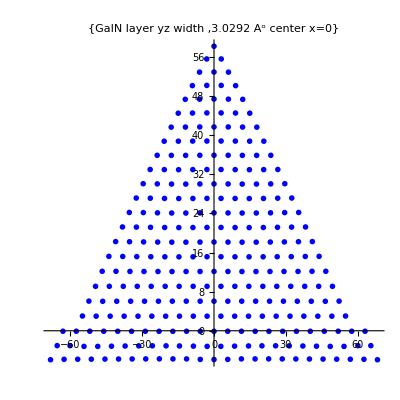

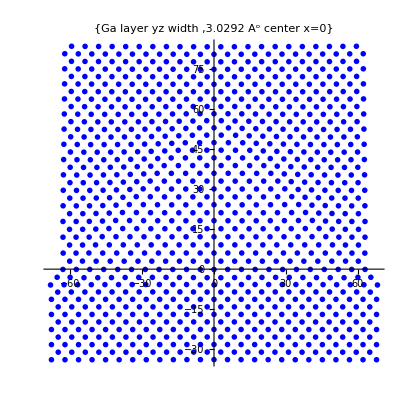

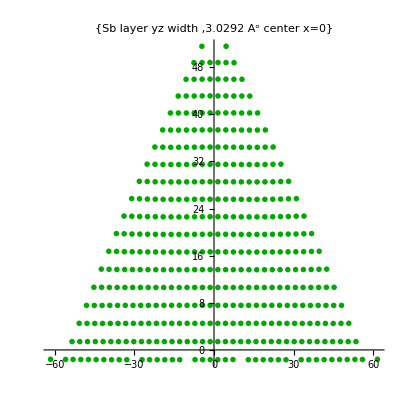

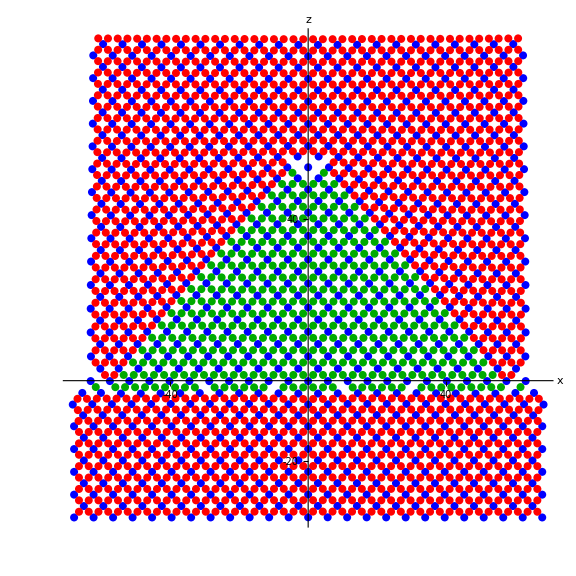

```mathematica
(*Collecting data for graphics 2D, plane yz (x=0), width,2*layer*)
YZ=Partition[Flatten[{GAYZ,GAinYZ,GAoutYZ,SBYZ,ASYZ}],2];
w1in=ListPlot[GAinYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"GaIN layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w1=ListPlot[GAYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All,PlotLabel->{"Ga layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w2=ListPlot[SBYZ,PlotStyle->{PointSize[0.01],Darker[Green]},PlotRange->All,PlotLabel->{"Sb layer yz width ",1*layer"A^o center x=0"},AspectRatio->1/1]
w3=ListPlot[ASYZ,PlotStyle->{PointSize[0.01],Red},PlotRange->All,PlotLabel->{"As layer yz width ",1*layer"A^o center x=0"}];
Show[w1,w2,w3,PlotRange->All,PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)",LabelStyle->Directive[Black,Bold,18],AxesLabel->{Style["  x (A^o)",18,Bold,Black,Italic],Style["  z (A^o)",18,Bold,Black,Italic]},Ticks->{{-40,40},{-20,0,40,80}}];
Show[w1,w2,w3,PlotRange->All,PlotLabel->"Relaxed: Ga(blue), As(red), Sb(green)",LabelStyle->Directive[Black,Bold,18],AxesLabel->{Style["  x (A^o)",18,Bold,Black,Italic],Style["  z (A^o)",18,Bold,Black,Italic]},Ticks->{{-40,40},{-20,0,40,80}}];

w1=ListPlot[GAYZ,PlotStyle->{PointSize[0.01],Blue},PlotRange->All];
w2=ListPlot[SBYZ,PlotStyle->{PointSize[0.01],Darker[Green]},PlotRange->All];
w3=ListPlot[ASYZ,PlotStyle->{PointSize[0.01],Red},PlotRange->All];

Show[w1,w2,w3,PlotRange->All,LabelStyle->Directive[Black,Bold,18],AxesLabel->{Style["x",18,Bold,Black,Italic],Style["z",18,Bold,Black,Italic]},Ticks->{{-40,40},{-20,0,40,80}},AspectRatio->1/1];

Show[w1,w2,w3,PlotRange->All,LabelStyle->Directive[Black,Bold,15],AxesLabel->{Style["x",14,Bold,Black,Italic],Style["z",14,Bold,Black,Italic]},Ticks->{{-50,50},{-20,0,40,80}},AspectRatio->1/1];

Show[w1,w2,w3,PlotRange->All,LabelStyle->Directive[Black,Bold,23],AxesLabel->{Style["x",28,Bold,Black,Italic],Style["z",28,Bold,Black,Italic]},Ticks->{{-40,40},{-20,40}},TicksStyle->Directive[Black,28],AspectRatio->1/1];
Show[%,ImageSize->Large]
```

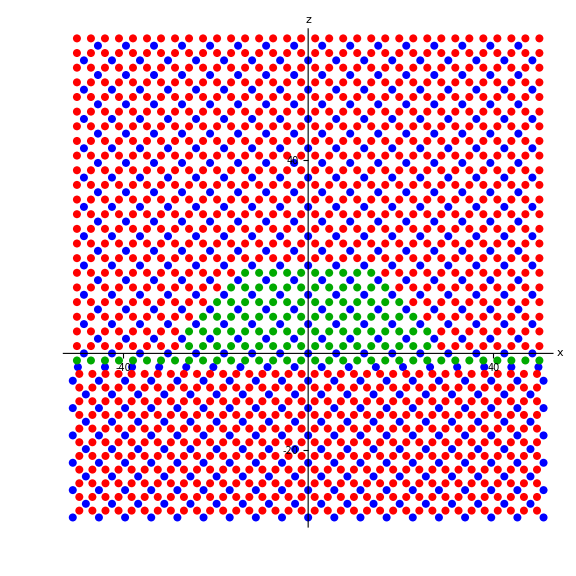
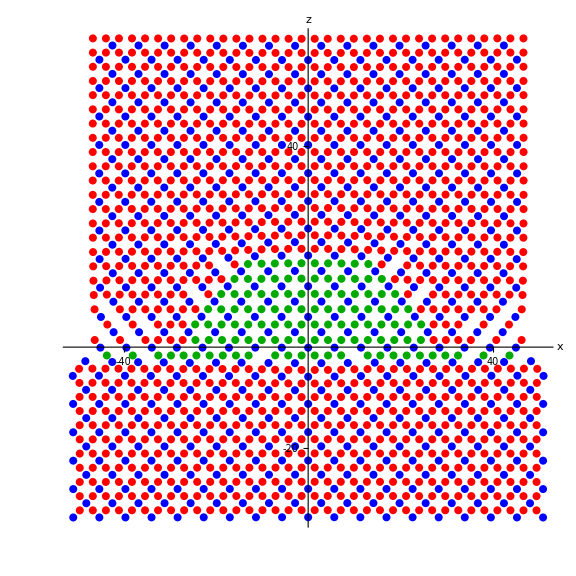
unrel: 4*a2/8  -Graphics-   rel: 4*a2/8 -Graphics-

# 1.5 Strain field calculus

## 1.5.1 In xy planes results

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;


(*z=0 plane*)
(*Ga*)epsxxplane0=Import["fort.1001"] ;(*for xy plane*)
(*Ga*)epsyyplane0=Import["fort.1002"]; (*for xy plane*)
(*Ga*)epszzplane0=Import["fort.1003"]; (*for xy plane*)
(*(*Ga*)epsxyplane0=Import["fort.1004"]; (*for xy plane*)*)
(*Ga*)epshydplane0=Import["fort.1007"]; (*for xy plane*)
epsxxplaneAll0=Import["fort.2011"]; (*for xy plane*)
epsyyplaneAll0=Import["fort.2012"]; (*for xy plane*)
epszzplaneAll0=Import["fort.2013"]; (*for xy plane*)
epshydplaneAll0=Import["fort.2017"]; (*for xy plane*)
(*LPXX0=ListPlot3D[epsxxplane0,PlotStyle->Directive[Opacity[0.3],Blue],PlotLabel->"epsxxplane0", PlotRange->{-0.07,0.03},Mesh->None]*)

LPXX0=ListPlot3D[epsxxplane0,PlotLabel->"epsxxplane0", PlotRange->All]
LPYY0=ListPlot3D[epsyyplane0,PlotLabel->"epsyyplane0", PlotRange->All]
LPZZ0=ListPlot3D[epszzplane0,PlotLabel->"epszzplane0", PlotRange->All]
LPHYD0=ListPlot3D[epshydplane0,PlotLabel->"epshydplane0", PlotRange->All]
(*Show[LPYY0,LPZZ0,LPHYD0, PlotRange->All, Mesh->None]*)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=zcord/2 plane, approx Rt/2 at hemitorus or h/2 at cone*)
(*Ga*)epsxxplane1=Import["fort.1101"]; (*for xy plane*)
(*Ga*)epsyyplane1=Import["fort.1102"]; (*for xy plane*)
(*Ga*)epszzplane1=Import["fort.1103"]; (*for xy plane*)
(*(*Ga*)epsxyplane1=Import["fort.1104"]; (*for xy plane*)*)
(*Ga*)epshydplane1=Import["fort.1107"]; (*for xy plane*)
epsxxplaneAll1=Import["fort.2111"]; (*for xy plane*)
epsyyplaneAll1=Import["fort.2112"]; (*for xy plane*)
epszzplaneAll1=Import["fort.2113"]; (*for xy plane*)
epshydplaneAll1=Import["fort.2117"]; (*for xy plane*)
LPXX1=ListPlot3D[epsxxplane1,PlotLabel->"epsxxplane1", PlotRange->All];
LPYY1=ListPlot3D[epsyyplane1,PlotLabel->"epsyyplane1", PlotRange->All];
LPZZ1=ListPlot3D[epszzplane1,PlotLabel->"epszzplane1", PlotRange->All];
LPHYD1=ListPlot3D[epshydplane1,PlotLabel->"epshydplane1", PlotRange->All];

LPXXAll1=ListPlot3D[epsxxplaneAll1,PlotLabel->"ε_xx",LabelStyle->Directive[Black,Bold,16], PlotRange->All, Ticks->{{-50,0,50},{-50,0,50},{-0.04,0,0.04}}];
Show[%,ImageSize->Large]
LPAllYY1=ListPlot3D[epsyyplaneAll1,PlotLabel->"ε_yy",LabelStyle->Directive[Black,Bold,16], PlotRange->All, Ticks->{{-50,0,50},{-50,0,50},{-0.04,0,0.04}}];
Show[%,ImageSize->Large]
LPAllZZ1=ListPlot3D[epszzplaneAll1,PlotLabel->"ε_zz",LabelStyle->Directive[Black,Bold,16], PlotRange->All, Ticks->{{-50,0,50},{-50,0,50},{-0.05,0}}];
Show[%,ImageSize->Large]
LPAllHYD1=ListPlot3D[epshydplaneAll1,PlotLabel->"ε_hyd",LabelStyle->Directive[Black,Bold,16], PlotRange->All, Ticks->{{-50,0,50},{-50,0,50},{-0.1,0}}];
Show[%,ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=zcord/1 plane, approx Rt at hemitorus or h at cone*)
(*Ga*)epsxxplane2=Import["fort.1201"]; (*for xy plane*)
(*Ga*)epsyyplane2=Import["fort.1202"]; (*for xy plane*)
(*Ga*)epszzplane2=Import["fort.1203"]; (*for xy plane*)
(*(*Ga*)epsxyplane2=Import["fort.1204"]; (*for xy plane*)*)
(*Ga*)epshydplane2=Import["fort.1207"]; (*for xy plane*)
epsxxplaneAll2=Import["fort.2211"]; (*for xy plane*)
epsyyplaneAll2=Import["fort.2212"]; (*for xy plane*)
epszzplaneAll2=Import["fort.2213"]; (*for xy plane*)
epshydplaneAll2=Import["fort.2217"]; (*for xy plane*)

LPXX2=ListPlot3D[epsxxplane2,PlotLabel->"epsxxplane2", PlotRange->All]
LPYY2=ListPlot3D[epsyyplane2,PlotLabel->"epsyyplane2", PlotRange->All]
LPZZ2=ListPlot3D[epszzplane2,PlotLabel->"epszzplane2", PlotRange->All]
LPHYD2=ListPlot3D[epshydplane2,PlotLabel->"epshydplane2", PlotRange->All]

LPXXAll2=ListPlot3D[epsxxplaneAll2,PlotLabel->"ε_xx",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPYYAll2=ListPlot3D[epsyyplaneAll2,PlotLabel->"ε_yy",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPZZAll2=ListPlot3D[epszzplaneAll2,PlotLabel->"ε_zz",LabelStyle->Directive[Bold,Italic], PlotRange->All];
LPHYDAll2=ListPlot3D[epshydplaneAll2,LabelStyle->Directive[Bold,Italic],PlotLabel->"ε_hyd", PlotRange->All];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*z=3*zcord/2 plane, approx 3*Rt/2 at hemitorus or 3*h/2 at cone*)
(*Ga*)epsxxplane3=Import["fort.1301"]; (*for xy plane*)
(*Ga*)epsyyplane3=Import["fort.1302"]; (*for xy plane*)
(*Ga*)epszzplane3=Import["fort.1303"]; (*for xy plane*)
(*(*Ga*)epsxyplane3=Import["fort.1304"]; (*for xy plane*)*)
(*Ga*)epshydplane3=Import["fort.1307"]; (*for xy plane*)
epsxxplaneAll2=Import["fort.2311"]; (*for xy plane*)
epsyyplaneAll2=Import["fort.2312"]; (*for xy plane*)
epszzplaneAll2=Import["fort.2313"]; (*for xy plane*)
epshydplaneAll2=Import["fort.2317"]; (*for xy plane*)
LPXX3=ListPlot3D[epsxxplane3,PlotLabel->"epsxxplane3", PlotRange->All]
LPYY3=ListPlot3D[epsyyplane3,PlotLabel->"epsyyplane3", PlotRange->All]
LPZZ3=ListPlot3D[epszzplane3,PlotLabel->"epszzplane3", PlotRange->All]
LPHYD3=ListPlot3D[epshydplane3,PlotLabel->"epshydplane3", PlotRange->All]
```

Import::nffil: File not found during Import.

ListPlot3D::arrayerr: $Failed must be a valid array or a list of valid arrays.

ListPlot3D[$Failed,PlotLabel→epsxxplane3,PlotRange→All]

ListPlot3D::arrayerr: $Failed must be a valid array or a list of valid arrays.

ListPlot3D[$Failed,PlotLabel→epsyyplane3,PlotRange→All]

ListPlot3D::arrayerr: $Failed must be a valid array or a list of valid arrays.

ListPlot3D[$Failed,PlotLabel→epszzplane3,PlotRange→All]

ListPlot3D::arrayerr: $Failed must be a valid array or a list of valid arrays.

ListPlot3D[$Failed,PlotLabel→epshydplane3,PlotRange→All]

## 1.5.2 In z direction results: comparison with Grundmann & Barettin; cap thickness

1.5.2.1. Stier & Barettin results

-Graphics--Graphics--Graphics- -Graphics--Graphics-
Stier+PRB59-VFF
https://journals.aps.org/prb/abstract/10.1103/PhysRevB.59.5688

-Graphics--Graphics-

barettin2012-VFF

1.5.2.2a. details for graph data (only for InAs/GaAs core-shell where there is an assymetry on the boundary)CS20InAs-CSQD1-14

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v2\\Strain_VFF_v2"];
SetDirectory["C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v3\\Strain_VFF_v3"];
SetDirectory["C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\AS_Calc_v1\\AS_Calc_v1"];
SetDirectory["C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\AS_Calc_v1.11\\AS_Calc_v1.11"];
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;

(*Ga*)epsxx=Sort[Import["fort.3401"],#1[[1]]<#2[[1]]&]
(*Ga*)epsyy=Sort[Import["fort.3402"],#1[[1]]<#2[[1]]&];
(*Ga*) epszz=Sort[Import["fort.3403"],#1[[1]]<#2[[1]]&] ;
 (*Ga*)epshyd=Sort[Import["fort.3404"],#1[[1]]<#2[[1]]&];
```

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v2\\Strain_VFF_v2".

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v3\\Strain_VFF_v3".

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\AS_Calc_v1\\AS_Calc_v1".

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\AS_Calc_v1.11\\AS_Calc_v1.11".

{{-73.5936,0.000373371},{-67.9374,-0.0000904947},{-62.2766,0.000148638},{-56.6206,0.000480285},{-50.967,0.000943209},{-45.3162,0.00245742},{-39.6806,0.00519646},{-34.0721,0.00806512},{-28.4983,0.0135489},{-23.029,0.0296607},{-17.5879,-0.0177256},{-11.7653,-0.0312252},{-5.88462,-0.0283026},{1.67346×10^-14,-0.0291351},{5.88462,-0.0283026},{11.7653,-0.0312252},{17.5879,-0.0177256},{23.029,0.0296607},{28.4983,0.0135489},{34.0721,0.00806512},{39.6806,0.00519646},{45.3162,0.00245742},{50.967,0.000943209},{56.6206,0.000480285},{62.2766,0.000148638},{67.9374,-0.0000904947},{73.5936,0.0668658}}

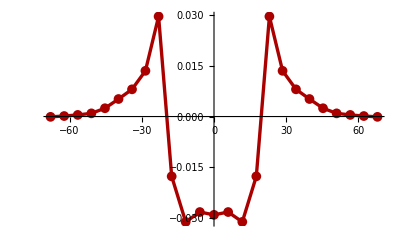

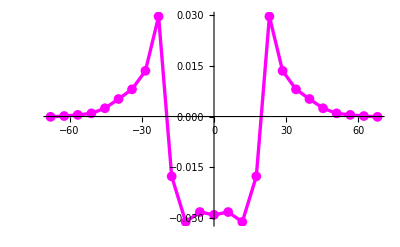

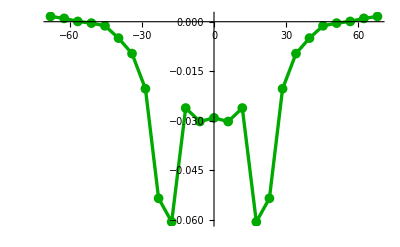

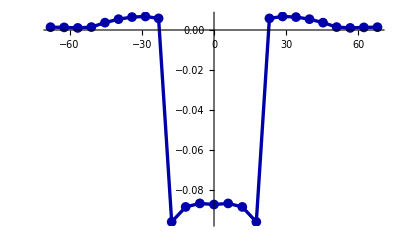

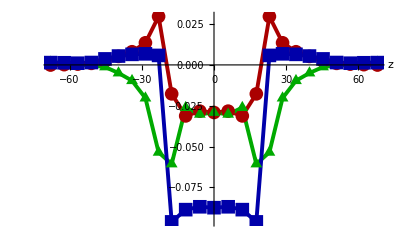

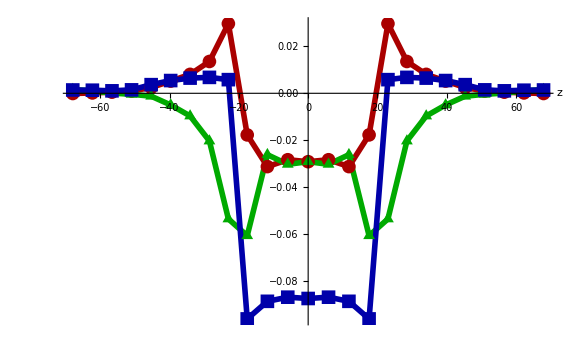

```mathematica
epsxx={{-67.9373795301974,-0.00009049465477180274},{-62.2765812162479,0.0001486378979993902},{-56.6205557825612,0.0004802851259029656},{-50.9670443174415,0.0009432093758632715},{-45.3162116930093,0.002457418503996098},{-39.6805644786936,0.005196463450100761},{-34.0721368083504,0.00806511932269087},{-28.498309341684,0.01354894011762002},{-23.0289724178192,0.02966070192711938},{-17.5879424841973,-0.0177255573471411},{-11.7653428095576,-0.03122518282027598},{-5.88461640424854,-0.0283025551955961},{1.673458785170687*^-14,-0.02913505950547335},{5.88461640424854,-0.0283025551956011},{11.7653428095576,-0.03122518282027942},{17.5879424841974,-0.01772555734714443},{23.0289724178193,0.02966070192712915},{28.4983093416839,0.0135489401176168},{34.0721368083503,0.00806511932268765},{39.6805644786936,0.00519646345008766},{45.3162116930093,0.002457418503964789},{50.9670443174414,0.0009432093758863641},{56.6205557825614,0.0004802851259046309},{62.2765812162479,0.0001486378979896202},{67.9373795301972,-0.00009049465471407114}};

epsyy={{-67.9373795301974,-0.00009049465471729079},{-62.2765812162479,0.0001486378979812936},{-56.6205557825612,0.0004802851258914193},{-50.9670443174415,0.0009432093758880294},{-45.3162116930093,0.002457418503976336},{-39.6805644786936,0.00519646345009743},{-34.0721368083504,0.008065119322676215},{-28.498309341684,0.01354894011761347},{-23.0289724178192,0.02966070192710428},{-17.5879424841973,-0.01772555734713444},{-11.7653428095576,-0.03122518282027775},{-5.88461640424854,-0.02830255519559954},{1.673458785170687*^-14,-0.02913505950547335},{5.88461640424854,-0.02830255519558944},{11.7653428095576,-0.03122518282027764},{17.5879424841974,-0.0177255573471311},{23.0289724178193,0.02966070192713248},{28.4983093416839,0.0135489401176299},{34.0721368083503,0.008065119322682654},{39.6805644786936,0.005196463450092545},{45.3162116930093,0.002457418504004424},{50.9670443174414,0.0009432093758781485},{56.6205557825614,0.0004802851259014113},{62.2765812162479,0.0001486378979714126},{67.9373795301972,-0.00009049465473549845}};

epszz={{-67.9373795301974,0.001591205643897739},{-62.2765812162479,0.001014959202693941},{-56.6205557825612,0.00008401817483420781},{-50.9670443174415,-0.0004249723080671092},{-45.3162116930093,-0.001240556574277754},{-39.6805644786936,-0.004966886808448548},{-34.0721368083504,-0.00966345249457086},{-28.498309341684,-0.02031928114498867},{-23.0289724178192,-0.05351065660549044},{-17.5879424841973,-0.06065376323465022},{-11.7653428095576,-0.02615549980742404},{-5.88461640424854,-0.03024576266556833},{1.673458785170687*^-14,-0.02913505950548334},{5.88461640424854,-0.03024576266556178},{11.7653428095576,-0.02615549980745691},{17.5879424841974,-0.06065376323465022},{23.0289724178193,-0.05351065660547401},{28.4983093416839,-0.02031928114497224},{34.0721368083503,-0.009663452494554428},{39.6805644786936,-0.004966886808432117},{45.3162116930093,-0.001240556574244892},{50.9670443174414,-0.0004249723080342466},{56.6205557825614,0.00008401817485075014},{62.2765812162479,0.001014959202710372},{67.9373795301972,0.001591205643881308}};

epshyd={{-67.9373795301974,0.001410216334408645},{-62.2765812162479,0.001312234998674625},{-56.6205557825612,0.001044588426628593},{-50.9670443174415,0.001461446443684192},{-45.3162116930093,0.003674280433694679},{-39.6805644786936,0.005426040091749643},{-34.0721368083504,0.006466786150796225},{-28.498309341684,0.006778599090244822},{-23.0289724178192,0.00581074724873322},{-17.5879424841973,-0.09610487792892575},{-11.7653428095576,-0.08860586544797777},{-5.88461640424854,-0.08685087305676398},{1.673458785170687*^-14,-0.08740517851643004},{5.88461640424854,-0.08685087305675232},{11.7653428095576,-0.08860586544801397},{17.5879424841974,-0.09610487792892575},{23.0289724178193,0.005810747248787621},{28.4983093416839,0.006778599090274465},{34.0721368083503,0.006466786150815876},{39.6805644786936,0.005426040091748088},{45.3162116930093,0.003674280433724322},{50.9670443174414,0.001461446443730266},{56.6205557825614,0.001044588426656792},{62.2765812162479,0.001312234998671405},{67.9373795301972,0.001410216334431738}};
VFFLBFGxx=ListPlot[{epsxx},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGxxyy=ListPlot[{epsyy},PlotRange->All,Joined->{True},PlotStyle->{{Magenta,Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGzz=ListPlot[{epszz},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGhyd=ListPlot[{epshyd},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Blue],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFG1=ListPlot[{epsxx,epsyy,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.006]},{Magenta,Thickness[0.006]},{Darker[Green],Thickness[0.006]},{Darker[Blue],Thickness[0.006]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,18],PlotLabel->"along z, ϵ_xx-brown,ϵ_yy-magenta,ϵ_zz-green,ϵ_hyd-blue"];

VFFLBFG1=ListPlot[{epsxx,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Blue],Thickness[0.007]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,16]]

Show[VFFLBFG1,ImageSize->Large]
```

1.5.2.2b. details for graph data (only for InAs/GaAs core-shell where there is an assymetry on the boundary)CS19InAs-CSQD1-13

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;

(*Ga*)epsxx=Sort[Import["fort.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy=Sort[Import["fort.3402"],#1[[1]]<#2[[1]]&];
(*Ga*) epszz=Sort[Import["fort.3403"],#1[[1]]<#2[[1]]&] ;
 (*Ga*)epshyd=Sort[Import["fort.3404"],#1[[1]]<#2[[1]]&]
```

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\AS_Calc_v2\\AS_Calc_v2".

{{-33.8738,0.000841201},{-28.2228,0.00130639},{-22.5733,0.00237883},{-16.9277,0.00435753},{-11.3066,-0.00476353},{-5.8874,-0.018397},{-0.112683,0.120746},{6.03054,-0.0913998},{12.1211,-0.0891733},{18.2428,0.0501088},{23.6187,-0.00337825},{29.087,0.00301503},{34.6435,0.00478071},{40.2541,0.00437177},{45.8844,0.00315582},{51.5248,0.00253347},{57.1693,0.000967407}}

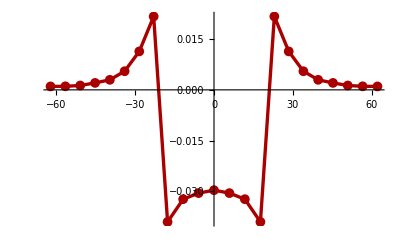

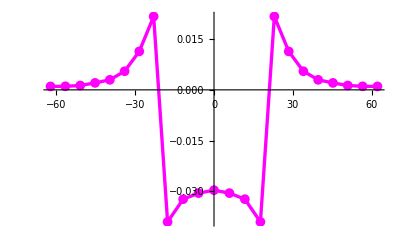

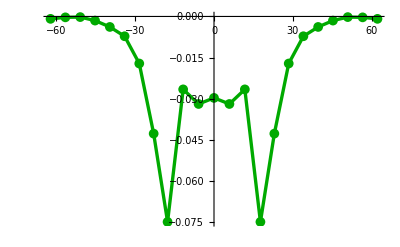

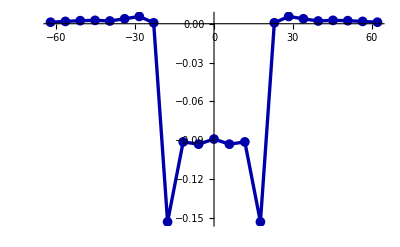

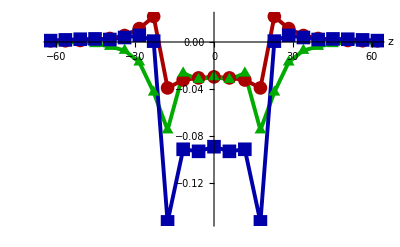

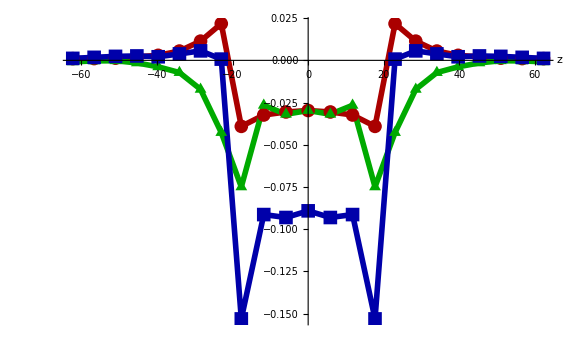

```mathematica
epsxx={{-62.2638907181408,0.00102146750829761},{-56.6122912521319,0.001055459941786727},{-50.9587373837709,0.001295371112402674},{-45.3110202877052,0.002057624404509448},{-39.6729545923253,0.002974484886197712},{-34.0499192057941,0.005516607762711387},{-28.4637583120061,0.01138978603339651},{-22.9840119936797,0.02173362593399557},{-17.6835758929223,-0.03909050531288449},{-11.7461109855846,-0.03236198225255027},{-5.87033701605768,-0.0305674494033622},{-9.37949164691146*^-16,-0.02970310274229493},{5.87033701605768,-0.03056744940336054},{11.7461109855846,-0.03236198225255027},{17.6835758929223,-0.03909050531287783},{22.9840119936797,0.02173362593401378},{28.4637583120062,0.01138978603339651},{34.0499192057942,0.005516607762722933},{39.6729545923254,0.002974484886186166},{45.3110202877053,0.002057624404501232},{50.9587373837708,0.001295371112407559},{56.6122912521318,0.001055459941793166},{62.2638907181408,0.00102146750829428}};

epsyy={{-62.2638907181408,0.001021467508277848},{-56.6122912521319,0.001055459941791612},{-50.9587373837709,0.00129537111240767},{-45.3110202877052,0.002057624404509448},{-39.6729545923253,0.002974484886192716},{-34.0499192057941,0.005516607762714718},{-28.4637583120061,0.01138978603339662},{-22.9840119936797,0.02173362593398913},{-17.6835758929223,-0.03909050531290437},{-11.7461109855846,-0.03236198225255027},{-5.87033701605768,-0.03056744940336054},{-9.37949164691146*^-16,-0.02970310274229826},{5.87033701605768,-0.0305674494033622},{11.7461109855846,-0.03236198225255027},{17.6835758929223,-0.03909050531289271},{22.9840119936797,0.02173362593400234},{28.4637583120062,0.01138978603339318},{34.0499192057942,0.005516607762716272},{39.6729545923254,0.002974484886191051},{45.3110202877053,0.002057624404515998},{50.9587373837708,0.001295371112406005},{56.6122912521318,0.001055459941786616},{62.2638907181408,0.001021467508289395}};

epszz={{-62.2638907181408,-0.0008699815150699647},{-56.6122912521319,-0.0003245439748764262},{-50.9587373837709,-0.000229455703154427},{-45.3110202877052,-0.001504940601563323},{-39.6729545923253,-0.003824313852535857},{-34.0499192057941,-0.007217674897713924},{-28.4637583120061,-0.01716199190561858},{-22.9840119936797,-0.04273161926056353},{-17.6835758929223,-0.07492891768513121},{-11.7461109855846,-0.02659336222042119},{-5.87033701605768,-0.03192121295644368},{-9.37949164691146*^-16,-0.02970310274229815},{5.87033701605768,-0.03192121295644368},{11.7461109855846,-0.02659336222042119},{17.6835758929223,-0.07492891768513121},{22.9840119936797,-0.04273161926058007},{28.4637583120062,-0.01716199190561914},{34.0499192057942,-0.007217674897730356},{39.6729545923254,-0.003824313852536967},{45.3110202877053,-0.001504940601596186},{50.9587373837708,-0.000229455703154427},{56.6122912521318,-0.0003245439748764262},{62.2638907181408,-0.0008699815150536444}};

epshyd={{-62.2638907181408,0.001172953501505494},{-56.6122912521319,0.001786375908701912},{-50.9587373837709,0.002361286521655917},{-45.3110202877052,0.002610308207455572},{-39.6729545923253,0.002124655919854571},{-34.0499192057941,0.00381554062771218},{-28.4637583120061,0.005617580161174543},{-22.9840119936797,0.0007356326074211689},{-17.6835758929223,-0.15310992831092},{-11.7461109855846,-0.09131732672552173},{-5.87033701605768,-0.09305611176316642},{-9.37949164691146*^-16,-0.08910930822689134},{5.87033701605768,-0.09305611176316642},{11.7461109855846,-0.09131732672552173},{17.6835758929223,-0.153109928310902},{22.9840119936797,0.0007356326074360459},{28.4637583120062,0.005617580161170546},{34.0499192057942,0.003815540627708849},{39.6729545923254,0.002124655919840249},{45.3110202877053,0.002610308207421044},{50.9587373837708,0.002361286521659137},{56.6122912521318,0.001786375908703355},{62.2638907181408,0.00117295350153003}};

VFFLBFGxx=ListPlot[{epsxx},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGxxyy=ListPlot[{epsyy},PlotRange->All,Joined->{True},PlotStyle->{{Magenta,Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGzz=ListPlot[{epszz},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFGhyd=ListPlot[{epshyd},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Blue],Thickness[0.006]}},PlotMarkers->{{●,10}}]

VFFLBFG1=ListPlot[{epsxx,epsyy,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.006]},{Magenta,Thickness[0.006]},{Darker[Green],Thickness[0.006]},{Darker[Blue],Thickness[0.006]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,18],PlotLabel->"along z, ϵ_xx-brown,ϵ_yy-magenta,ϵ_zz-green,ϵ_hyd-blue"];

VFFLBFG1=ListPlot[{epsxx,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Blue],Thickness[0.007]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,16]]

Show[VFFLBFG1,ImageSize->Large]
```

1.5.2.3. graphs for all QD shapes except core-shell

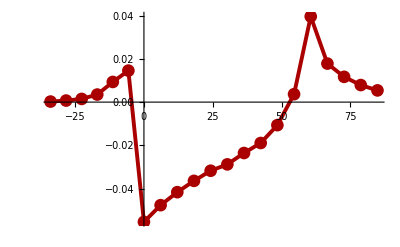

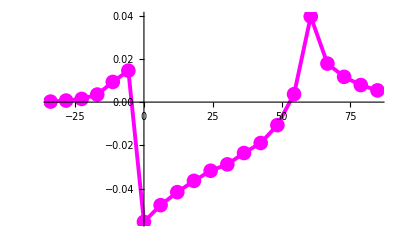

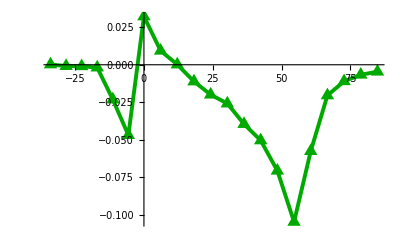

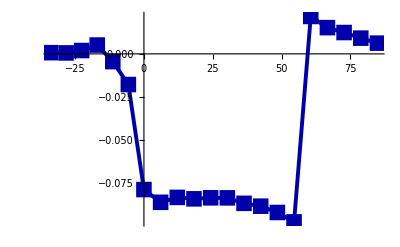

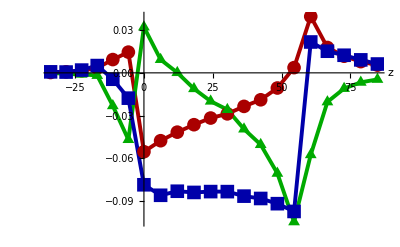

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;

(*Ga*)epsxx=Sort[Import["fort.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy=Sort[Import["fort.3402"],#1[[1]]<#2[[1]]&];
 epszz=Sort[Import["fort.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd=Sort[Import["fort.3404"],#1[[1]]<#2[[1]]&];
epsxxAll=Sort[Import["fort.3411"],#1[[1]]<#2[[1]]&];
 epsyyAll=Sort[Import["fort.3412"],#1[[1]]<#2[[1]]&];  epszzAll=Sort[Import["fort.3413"],#1[[1]]<#2[[1]]&];epshydAll=Sort[Import["fort.3414"],#1[[1]]<#2[[1]]&];
ListPlot[{epsxx,epsyy}];

VFFLBFGxx=ListPlot[{epsxx},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.007]}},PlotMarkers->{{●,13}}]

VFFLBFGxxyy=ListPlot[{epsyy},PlotRange->All,Joined->{True},PlotStyle->{{Magenta,Thickness[0.007]}},PlotMarkers->{{●,15}}]

VFFLBFGzz=ListPlot[{epszz},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.007]}},PlotMarkers->{{▲,16}}]


VFFLBFGhyd=ListPlot[{epshyd},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Blue],Thickness[0.007]}},PlotMarkers->{{■,16}}]

VFFLBFG1=ListPlot[{epsxx,epsyy,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style["Strain",20,Bold,Black,Italic]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.006]},{Magenta,Thickness[0.006]},{Darker[Green],Thickness[0.006]},{Darker[Blue],Thickness[0.006]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,18],PlotLabel->"along z, ϵ_xx-brown,ϵ_yy-magenta,ϵ_zz-green,ϵ_hyd-blue"];

VFFLBFG1=ListPlot[{epsxx,epszz,epshyd},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Blue],Thickness[0.007]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,16]]
```

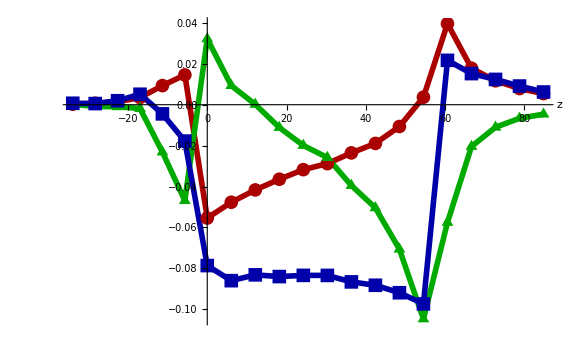

```mathematica
Show[VFFLBFG1,ImageSize->Large]
```

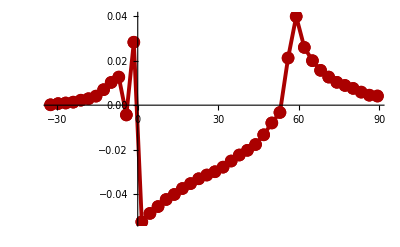

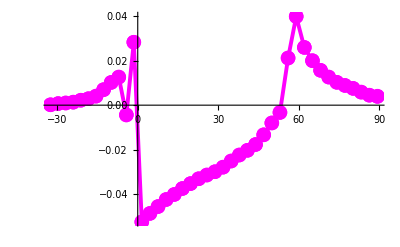

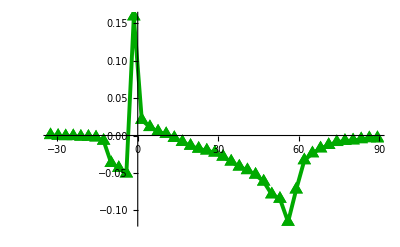

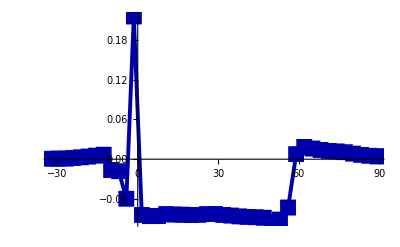

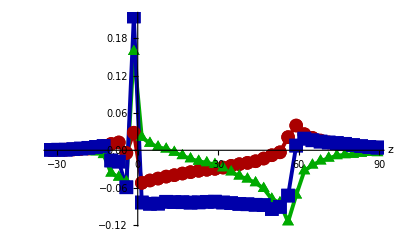

```mathematica
VFFLBFGxxAll=ListPlot[{epsxxAll},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Red],Thickness[0.007]}},PlotMarkers->{{●,13}}]

VFFLBFGxxyyAll=ListPlot[{epsyyAll},PlotRange->All,Joined->{True},PlotStyle->{{Magenta,Thickness[0.007]}},PlotMarkers->{{●,15}}]

VFFLBFGzzAll=ListPlot[{epszzAll},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Green],Thickness[0.007]}},PlotMarkers->{{▲,16}}]


VFFLBFGhydAll=ListPlot[{epshydAll},PlotRange->All,Joined->{True},PlotStyle->{{Darker[Blue],Thickness[0.007]}},PlotMarkers->{{■,16}}]

VFFLBFG1All=ListPlot[{epsxxAll,epsyyAll,epszzAll,epshydAll},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style["Strain",20,Bold,Black,Italic]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.006]},{Magenta,Thickness[0.006]},{Darker[Green],Thickness[0.006]},{Darker[Blue],Thickness[0.006]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,18],PlotLabel->"along z, ϵ_xx-brown,ϵ_yy-magenta,ϵ_zz-green,ϵ_hyd-blue"];

VFFLBFG1All=ListPlot[{epsxxAll,epszzAll,epshydAll},PlotRange->All,AxesLabel->{Style[" z",20,Bold,Black,Italic],Style[""]},PlotMarkers->{{●,14},{▲,14},{■,14}},PlotStyle->{{Darker[Red],Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Darker[Blue],Thickness[0.007]}},Joined->{True,True,True},LabelStyle->Directive[Black,Bold,16]]
```

1.5.2.4. cap thickness for P42; Figs.: 5c, 5d, 5e

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v3\\P42-67812"];
(*P42-1101066G10:*)
(*Ga*)epsxx6=Sort[Import["fort6-10.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy6=Sort[Import["fort6-10.3402"],#1[[1]]<#2[[1]]&];
 epszz6=Sort[Import["fort6-10.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd6=Sort[Import["fort6-10.3404"],#1[[1]]<#2[[1]]&];

(*P42-1101066G9:*)
(*Ga*)epsxx6=Sort[Import["fort6.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy6=Sort[Import["fort6.3402"],#1[[1]]<#2[[1]]&];
 epszz6=Sort[Import["fort6.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd6=Sort[Import["fort6.3404"],#1[[1]]<#2[[1]]&];

(*P42-1101067G10:*)
(*Ga*)epsxx7=Sort[Import["fort7.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy7=Sort[Import["fort7.3402"],#1[[1]]<#2[[1]]&];
 epszz7=Sort[Import["fort7.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd7=Sort[Import["fort7.3404"],#1[[1]]<#2[[1]]&];

(*P42-1101068G10:*)
(*Ga*)epsxx8=Sort[Import["fort8.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy8=Sort[Import["fort8.3402"],#1[[1]]<#2[[1]]&];
 epszz8=Sort[Import["fort8.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd8=Sort[Import["fort8.3404"],#1[[1]]<#2[[1]]&];

(*P42-11010612G10:*)
(*Ga*)epsxx12=Sort[Import["fort12.3401"],#1[[1]]<#2[[1]]&];
(*Ga*)epsyy12=Sort[Import["fort12.3402"],#1[[1]]<#2[[1]]&];
 epszz12=Sort[Import["fort12.3403"],#1[[1]]<#2[[1]]&] ;
 epshyd12=Sort[Import["fort12.3404"],#1[[1]]<#2[[1]]&];

VFFLBFGxx67812=ListPlot[{epsxx7,epsxx7,epsxx12,epsxx12},PlotRange->All,AxesLabel->{Style[" z",26,Bold,Black,Italic],Style["ϵ_xx=ϵ_yy"]},PlotMarkers->{{●,18},{●,18},{■,18},{■,18}},PlotStyle->{{Red,Thickness[0.009]},{Red,Thickness[0.009]},{Darker[Blue],Thickness[0.009]},{Darker[Blue],Thickness[0.009]}},Joined->{True,True,True,True},Ticks->{{-30,20,40,60},{-0.08,-0.04, 0.04}},LabelStyle->Directive[Black,Bold,23]];
Show[VFFLBFGxx67812,ImageSize->Large]

VFFLBFGzz67812=ListPlot[{epszz7,epszz7,epszz12,epszz12},PlotRange->All,AxesLabel->{Style[" z",26,Bold,Black,Italic],Style["ϵ_zz"]},PlotMarkers->{{●,18},{●,18},{■,18},{■,18}},PlotStyle->{{Red,Thickness[0.009]},{Red,Thickness[0.009]},{Darker[Blue],Thickness[0.009]},{Darker[Blue],Thickness[0.009]}},Joined->{True,True,True,True},Ticks->{{-30,20,40,60},{-0.08,-0.04, 0.04}},LabelStyle->Directive[Black,Bold,23]];
Show[VFFLBFGzz67812,ImageSize->Large]

VFFLBFGhyd67812=ListPlot[{epshyd7,epshyd7,epshyd12,epshyd12},PlotRange->All,AxesLabel->{Style[" z",26,Bold,Black,Italic],Style["ϵ_hyd"]},PlotMarkers->{{●,18},{●,18},{■,18},{■,18}},PlotStyle->{{Red,Thickness[0.009]},{Red,Thickness[0.009]},{Darker[Blue],Thickness[0.009]},{Darker[Blue],Thickness[0.009]}},Joined->{True,True,True,True},Ticks->{{-30,20,40,60},{-0.1,-0.06,-0.02, 0.02}},LabelStyle->Directive[Black,Bold,23]];
Show[VFFLBFGhyd67812,ImageSize->Large]
```

SetDirectory::cdir: Cannot set current directory to "C:\\Users\\Tiberius\\Desktop\\Strain_Codes\\Strain_VFF_v3\\P42-67812".

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

Import::nffil: File not found during Import.

Sort::normal: Nonatomic expression expected at position 1 in Sort[$Failed, #1 ⟦ 1 ⟧ < #2 ⟦ 1 ⟧ &].

-Graphics-

-Graphics-

-Graphics-

# 1.6 Stier & Grundmann comparison

## 1.6.1 Stier & Grundmann comparison

Stier+PRB59-VFF-piezo.pdf
b=13.6nm

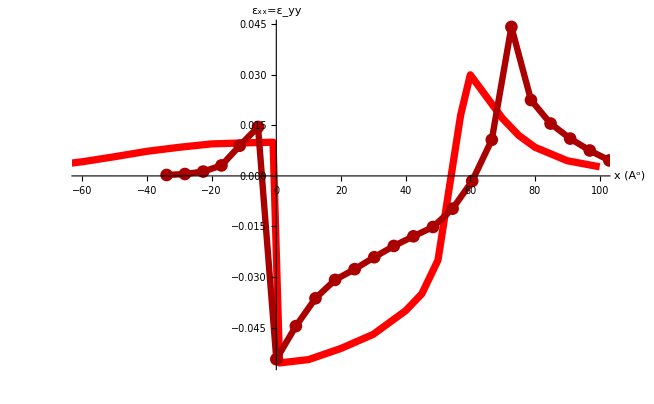

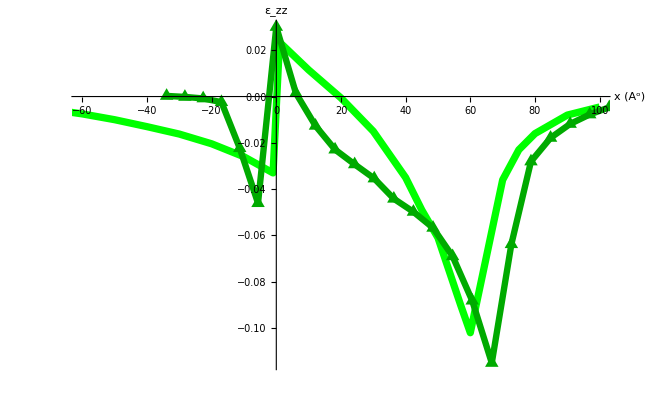

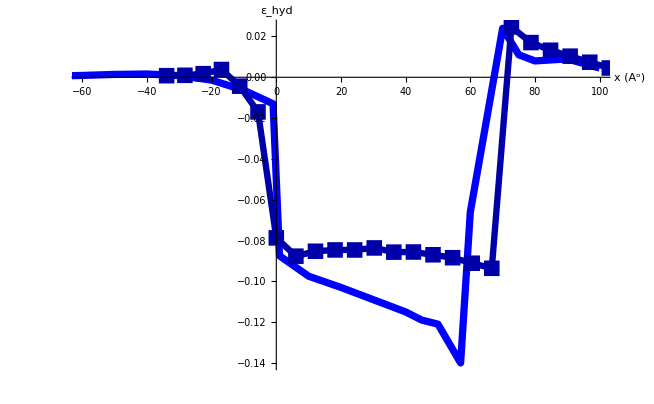

```mathematica
(*Stier+PRB59-VFF-piezo.pdf*)
epsxxEx={{-7,0.3},{-6,0.42},{-5,0.57},{-4,0.73},{-3,0.85},{-2,0.95},{-1,0.98},{-0.1,1},{0.1,-5.55},{1,-5.45},{2,-5.12},{3,-4.7},{4,-4},{4.5,-3.5},{4.75,-3.},{5,-2.5},{5.7,1.8},{6,3.},{7,1.7},{7.5,1.2},{8,0.85},{9,0.45},{10,0.27}};
Dimx=Dimensions[epsxxEx][[1]];
epsxxExRow=10*epsxxEx[[All,1]];
epsxxExCol=epsxxEx[[All,2]]/100.;
epsxxEx=Table[{epsxxExRow[[i]],epsxxExCol[[i]]},{i,1,Dimx}];
Ex=ListLinePlot[epsxxEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.008],Red]];

epszzEx={{-7,-0.55},{-6,-0.75},{-5,-1.0},{-4,-1.3},{-3,-1.62},{-2,-2.04},{-1,-2.6},{-0.1,-3.3},{0.1,2.35},{1,1.15},{2,-0.06},{3,-1.5},{4,-3.5},{4.5,-4.9},{5,-6.1},{5.7,-9},{6,-10.2},{7,-3.6},{7.5,-2.3},{8,-1.6},{9,-0.8},{10,-0.45}};
Dimz=Dimensions[epszzEx][[1]];
epszzExRow=10*epszzEx[[All,1]];
epszzExCol=epszzEx[[All,2]]/100.;
epszzEx=Table[{epszzExRow[[i]],epszzExCol[[i]]},{i,1,Dimz}];
Ez=ListLinePlot[epszzEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.008],Green]];


epsEhydEx=Table[{epszzExRow[[i]],epszzExCol[[i]]+2*epsxxExCol[[i]]},{i,1,Dimz}];
Ehyd=ListLinePlot[epsEhydEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.008],Blue]];

Show[Ex,Ez,Ehyd,PlotRange->All];
Show[{Ex,VFFLBFGxx},PlotRange->{{-60,100},All},AxesLabel->{Style["  x (A^o)",15,Bold,Black,Italic],Style["ε_xx=ε_yy",15,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,12]]
Show[{Ez,VFFLBFGzz},PlotRange->{{-60,100},All},AxesLabel->{Style["  x (A^o)",15,Bold,Black,Italic],Style["ε_zz",15,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,12]]
Show[{Ehyd,VFFLBFGhyd},PlotRange->{{-60,100},All},AxesLabel->{Style["  x (A^o)",15,Bold,Black,Italic],Style["ε_hyd",15,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,12]]
Show[{Ez,VFFLBFGzz},PlotRange->All];
Show[{Ehyd,VFFLBFGhyd},PlotRange->All];
Show[Ex,Ez,Ehyd,VFFLBFGxx,VFFLBFGzz,VFFLBFGhyd,PlotRange->All];
```

Grundmann+PRB52
b=12nm
better match if using write(3401,*)rp(m,3),epsxx(m) in AS_Calc_v1;

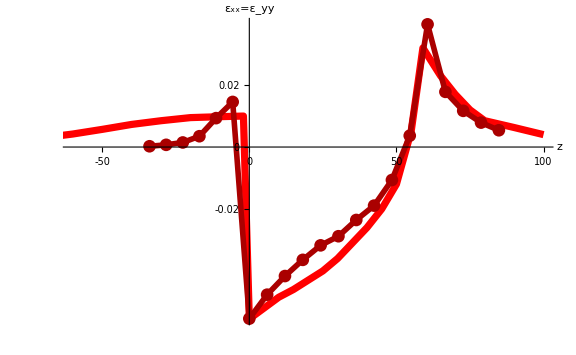

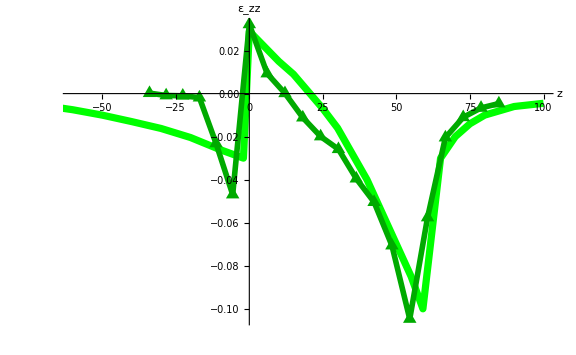

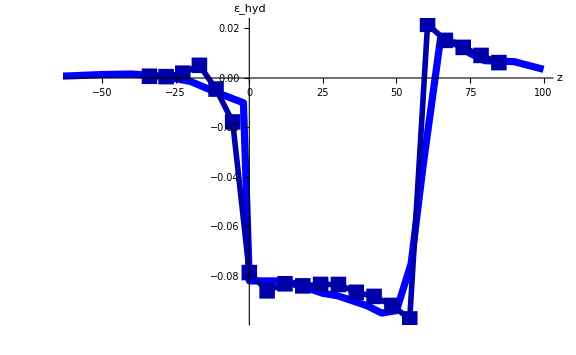

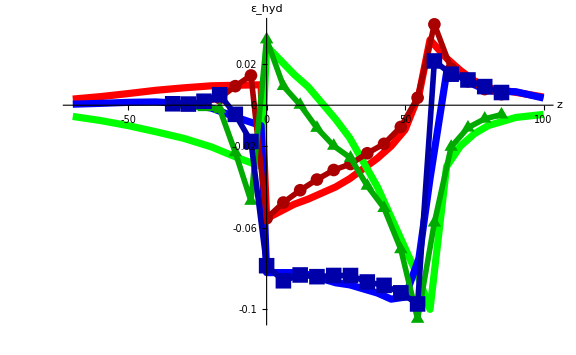

```mathematica
(*Grundmann.pdf*)
(*-----------------------------*)
(*1*)
epsxxEx={{-70,0.003},{-60,0.0042},{-50,0.0057},{-40,0.0073},{-30,0.0085},{-20,0.0095},{-10,0.0098},{-2.,0.01},{0,-0.0555},{10,-0.0485},{15,-0.046},{20,-0.042},{25,-0.0385},{30,-0.0345},{35,-0.031},{40,-0.027},{45.,-0.022},{50,-0.012},{55,0.005},{59,0.032},{65,0.023},{70,0.017},{75.,0.012},{80,0.0085},{90,0.0063},{100,0.004}};
(*-----------------------------*)
(*2*)
epsxxEx={{-70,0.003},{-60,0.0042},{-50,0.0057},{-40,0.0073},{-30,0.0085},{-20,0.0095},{-10,0.0098},{-2.,0.01},{0,-0.0555},{10,-0.0485},{15,-0.046},{20,-0.042},{25,-0.0385},{30,-0.0345},{35,-0.031},{40,-0.026},{45.,-0.02},{50,-0.012},{55,0.005},{59,0.032},{65,0.023},{70,0.017},{75.,0.012},{80,0.0085},{90,0.0063},{100,0.004}};
(*-----------------------------*)
(*-----------------------------*)
(*3*)
epsxxEx={{-70,0.003},{-60,0.0042},{-50,0.0057},{-40,0.0073},{-30,0.0085},{-20,0.0095},{-10,0.0098},{-2.,0.01},{0,-0.0555},{10,-0.0485},{15,-0.046},{20,-0.043},{25,-0.04},{30,-0.036},{35,-0.031},{40,-0.026},{45.,-0.02},{50,-0.012},{55,0.005},{59,0.032},{65,0.023},{70,0.017},{75.,0.012},{80,0.0085},{90,0.0063},{100,0.004}};
(*-----------------------------*)

Dimx=Dimensions[epsxxEx][[1]];
epsxxExRow=epsxxEx[[All,1]]*1;
epsxxExCol=epsxxEx[[All,2]];
epsxxEx=Table[{epsxxExRow[[i]],epsxxExCol[[i]]},{i,1,Dimx}];
Ex=ListLinePlot[epsxxEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.009],Red]];
(*-----------------------------*)
(*1*)
epszzEx={{-70.,-0.0055},{-60.,-0.0075},{-50.,-0.01},{-40.,-0.013},{-30.,-0.0162},{-20.,-0.0204},{-10.,-0.026},{-2.,-0.03},{0,0.029},{10,0.015},{15,0.009},{20,0.001},{25,-0.007},{30,-0.016},{35,-0.024},{40,-0.035},{45.,-0.048},{50,-0.07},{55,-0.085},{59,-0.095},{65,-0.03},{70.,-0.02},{75.,-0.014},{80.,-0.010},{90.,-0.006},{100.,-0.0045}};
(*-----------------------------*)
(*2*)
epszzEx={{-70.,-0.0055},{-60.,-0.0075},{-50.,-0.01},{-40.,-0.013},{-30.,-0.0162},{-20.,-0.0204},{-10.,-0.026},{-2.,-0.03},{0,0.029},{10,0.015},{15,0.009},{20,0.001},{25,-0.007},{30,-0.016},{35,-0.025},{40,-0.037},{45.,-0.051},{50,-0.071},{55,-0.095},{59,-0.07},{65,-0.03},{70.,-0.02},{75.,-0.014},{80.,-0.010},{90.,-0.006},{100.,-0.0045}};
(*-----------------------------*)
(*-----------------------------*)
(*3*)
epszzEx={{-70.,-0.0055},{-60.,-0.0075},{-50.,-0.01},{-40.,-0.013},{-30.,-0.0162},{-20.,-0.0204},{-10.,-0.026},{-2.,-0.03},{0,0.029},{10,0.015},{15,0.009},{20,0.001},{25,-0.007},{30,-0.016},{35,-0.028},{40,-0.04},{45.,-0.055},{50,-0.07},{55,-0.085},{59,-0.1},{65,-0.03},{70.,-0.02},{75.,-0.014},{80.,-0.010},{90.,-0.006},{100.,-0.0045}};
(*-----------------------------*)

Dimz=Dimensions[epszzEx][[1]];
epszzExRow=epszzEx[[All,1]]*1;
epszzExCol=epszzEx[[All,2]];
epszzEx=Table[{epszzExRow[[i]],epszzExCol[[i]]},{i,1,Dimz}];
Ez=ListLinePlot[epszzEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.009],Green]];

epsEhydEx=Table[{epszzExRow[[i]],epszzExCol[[i]]+2*epsxxExCol[[i]]},{i,1,Dimz}];
Ehyd=ListLinePlot[epsEhydEx,Joined->True, Mesh->None,PlotRange->All,PlotStyle->Directive[Thickness[0.009],Blue]];

Show[Ex,Ez,Ehyd,PlotRange->All];
Show[{Ex,VFFLBFGxx},PlotRange->{{-60,100},All},AxesLabel->{Style["  z",19,Bold,Black,Italic],Style["ε_xx=ε_yy",19,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,19],Ticks->{{-50,0,50,100},{-0.1,-0.06,-0.02,0,0.02}}];
Show[%,ImageSize->Large]

Show[{Ez,VFFLBFGzz},PlotRange->{{-60,100},All},AxesLabel->{Style["  z",19,Bold,Black,Italic],Style["ε_zz",19,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,19]];
Show[%,ImageSize->Large]

Show[{Ehyd,VFFLBFGhyd},PlotRange->{{-60,100},All},AxesLabel->{Style["  z",19,Bold,Black,Italic],Style["ε_hyd",19,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,19]];
Show[%,ImageSize->Large]

Show[{Ez,VFFLBFGzz},PlotRange->All];
Show[{Ehyd,VFFLBFGhyd},PlotRange->All];
Show[Ex,Ez,Ehyd,VFFLBFGxx,VFFLBFGzz,VFFLBFGhyd,PlotRange->All,AxesLabel->{Style["  z",19,Bold,Black,Italic],Style["ε_hyd",19,Bold,Black,Italic]},LabelStyle->Directive[Black,Bold,19],Ticks->{{-50,0,50,100},{-0.1,-0.06,-0.02,0,0.02}}];
Show[%,ImageSize->Large]
```

## 1.6.2 Setting of radiuscut1, see Introduction (dij<radiuscut1)

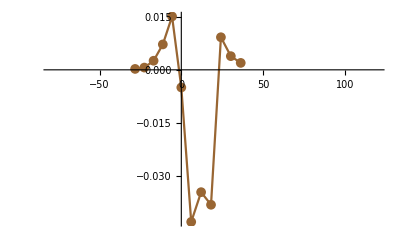
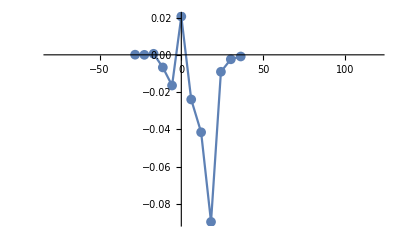
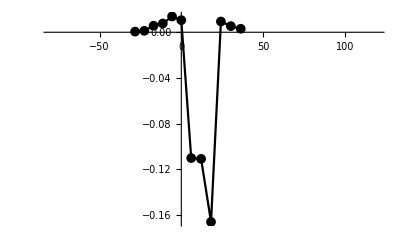
radiuscut1=2.7,  factr=1d+12
-Graphics--Graphics-
-Graphics-

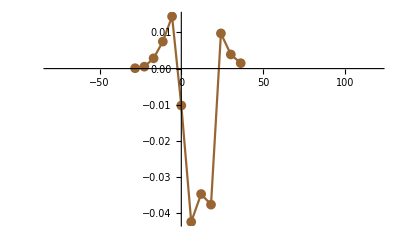
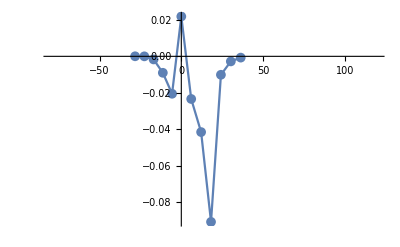
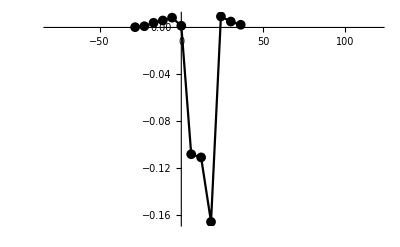
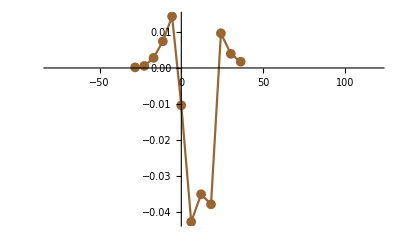
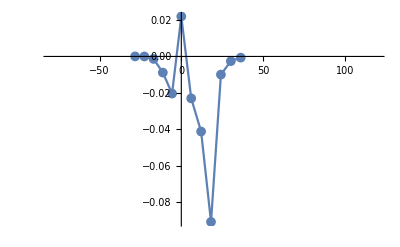
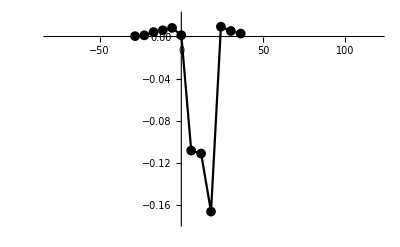
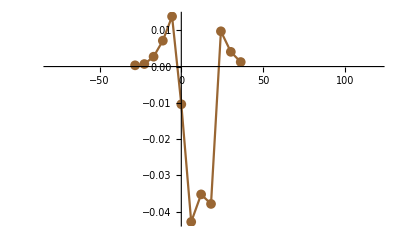
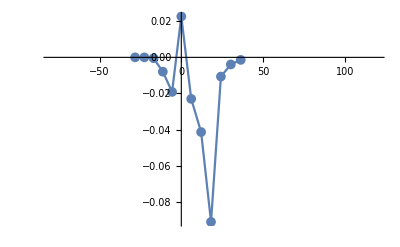
radiuscut1=3, factr = 1 d + 10
-Graphics--Graphics-
-Graphics-
radiuscut1=3, factr = 1 d + 11
-Graphics--Graphics-
-Graphics-
radiuscut1=3, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

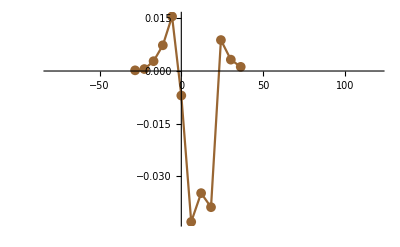
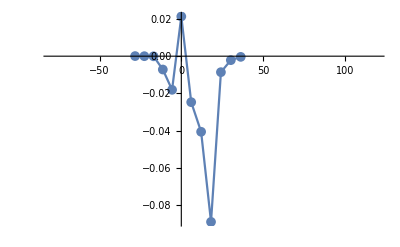
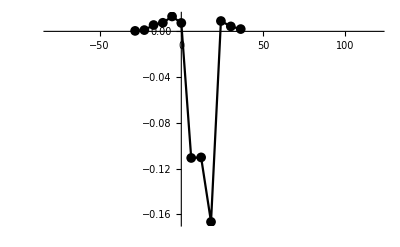
radiuscut1=2.65,  factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

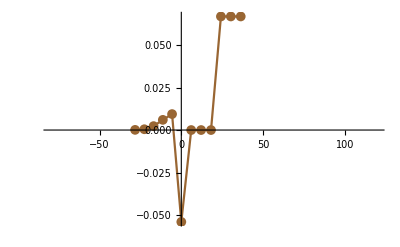
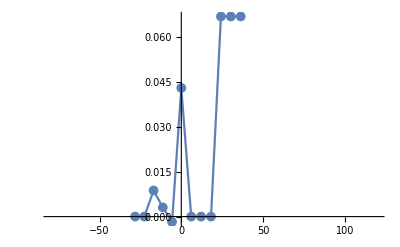
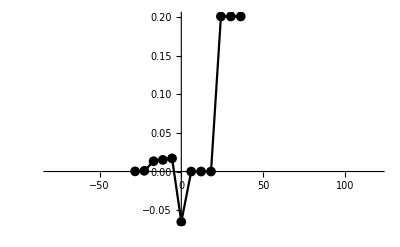
radiuscut1=2.62,  factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

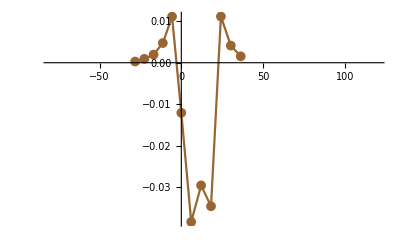
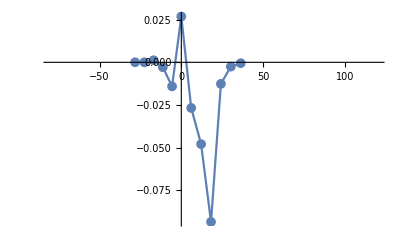
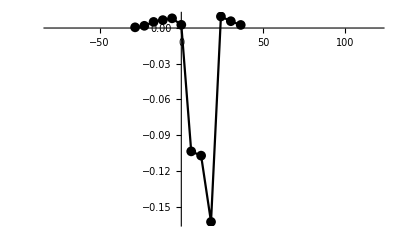
radiuscut1=3.3, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

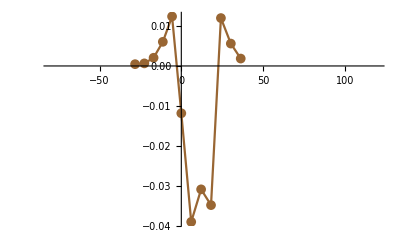
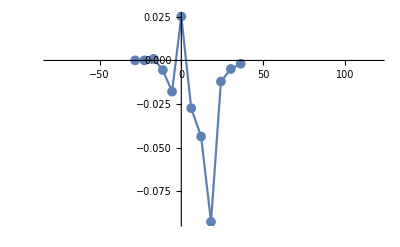
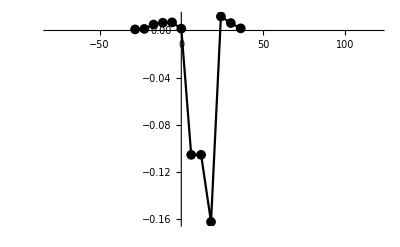
radiuscut1=3.2, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

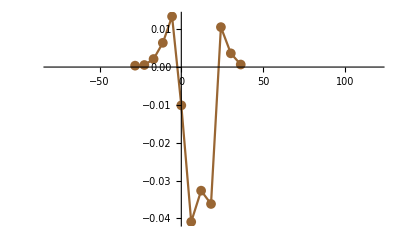
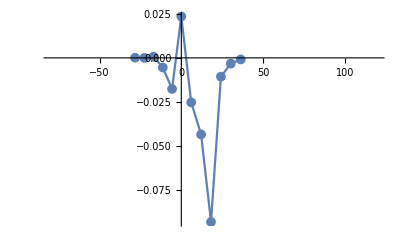
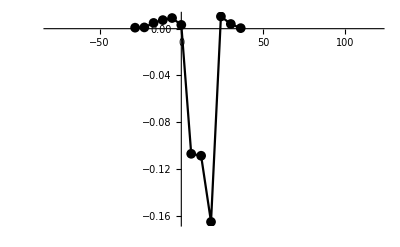
radiuscut1=3.1, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

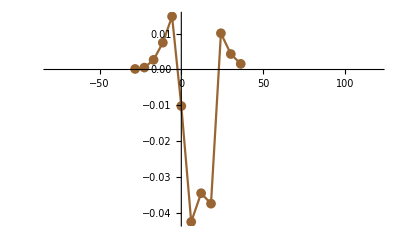
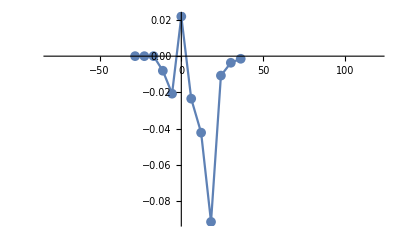
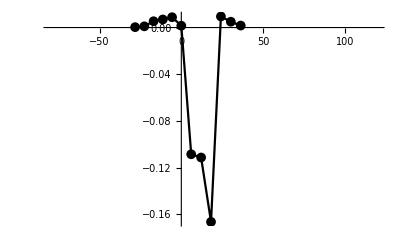
radiuscut1=2.9, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

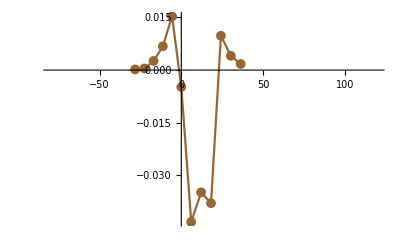
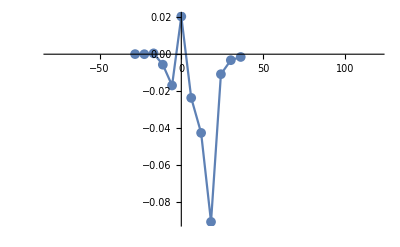
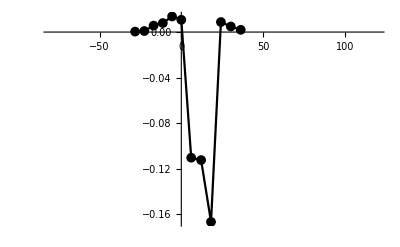
radiuscut1=2.8, factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

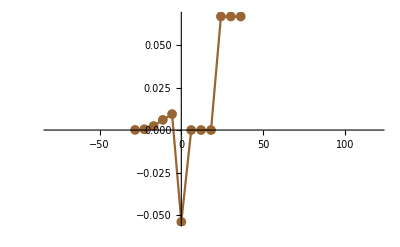
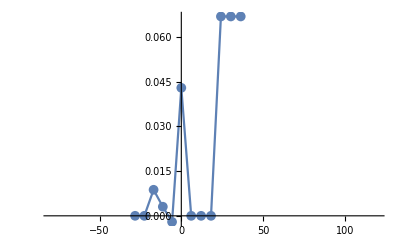
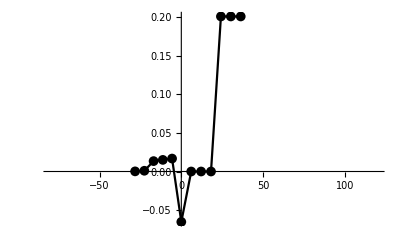
radiuscut1=2.6,  factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

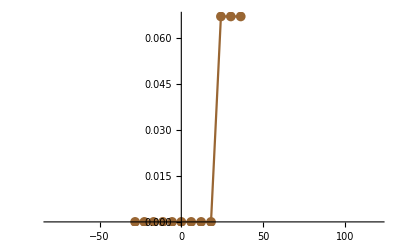
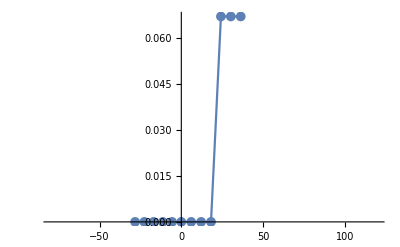
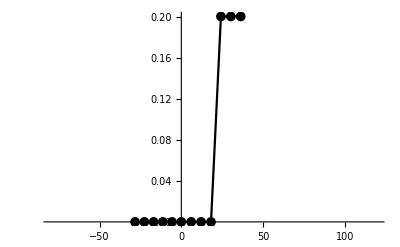
radiuscut1=2.3,  factr = 1 d + 12
-Graphics--Graphics-
-Graphics-

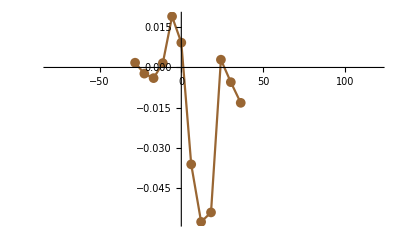
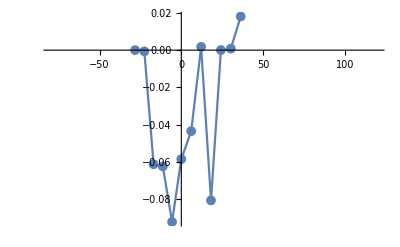
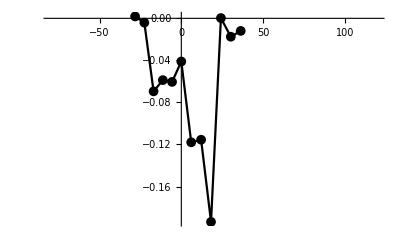
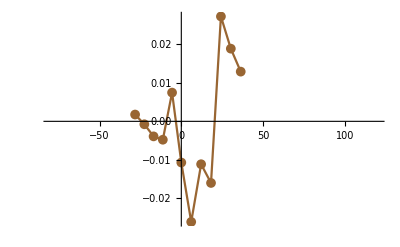
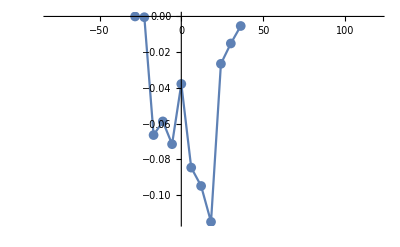
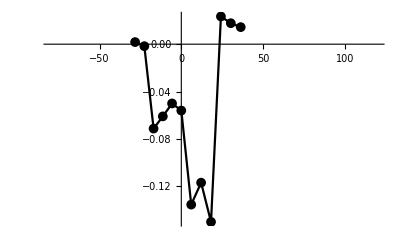
radiuscut1=5, factr=1d+12
-Graphics--Graphics-
-Graphics-
radiuscut1=5, factr=1d+11
-Graphics--Graphics-
-Graphics-

# 1.7 Misfit dislocations

## 1.7.1 InAs/GaAs QDs For all QDs. It gives up view for core-shell InAs/GaAs

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;
Clear[MDGa,MDGa1]
(*Ga!!!*)(*mdGa=Import["temp1502.dat"];*)
mdGa=Import["fort.502"];
mdGa1=Import["fort.502"];
dimGa=Dimensions[mdGa][[1]]
dimGa1=Dimensions[mdGa][[1]]

zmax=200;
mdGa01={};
Do[
If[0<mdGa1[[i,3]]≤zmax&&Abs[mdGa1[[i,1]]]≤200&&Abs[mdGa1[[i,2]]]≤200,MDGa1=Append[mdGa01,mdGa[[i]]];mdGa01=MDGa1],
 {i,1,dimGa1}];
MDGa1[[1,3]];
MDGa1;
Dimensions[MDGa1][[1]]
GaList1=ListPointPlot3D[MDGa1,PlotStyle->Directive[Blue,PointSize[0.007],Lighting->Automatic],PlotRange->All]
```

16398

16398

7220

-Graphics3D-

```mathematica
mdGa0={};
Do[
If[-10≤mdGa[[i,3]]≤zmax&&Abs[mdGa[[i,1]]]≤200&&Abs[mdGa[[i,2]]]≤200,MDGa=Append[mdGa0,mdGa[[i]]];mdGa0=MDGa],
 {i,1,dimGa}];
MDGa[[1,3]];
MDGa;
Dimensions[MDGa][[1]]
GaList=ListPointPlot3D[MDGa,PlotStyle->Directive[Blue,PointSize[0.007]],PlotRange->All]
```

12346

-Graphics3D-

```mathematica
Clear[MDSb]
(*Sb*)(*mdSb=Import["temp1503.dat"];*)
mdSb=Import["fort0032.503"];
dimSb=Dimensions[mdSb][[1]]

mdSb=Import["fort.503"];
dimSb=Dimensions[mdSb][[1]]



mdSb0={};
Do[
If[-10≤mdSb[[i,3]]≤zmax&&Abs[mdSb[[i,1]]]≤200&&Abs[mdSb[[i,2]]]≤200,MDSb=Append[mdSb0,mdSb[[i]]];mdSb0=MDSb],
 {i,1,dimSb}];
MDSb[[1,3]];
MDSb;
SbList=ListPointPlot3D[MDSb,PlotStyle->Directive[Darker[Green],PointSize[0.009]],PlotRange->All]
```

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

1814

-Graphics3D-

```mathematica
3
```

3

```mathematica
Clear[MDAs]
(*As*)(*mdAs=Import["temp1504.dat"];*)
mdAs=Import["fort.504"];
dimAs=Dimensions[mdAs][[1]]

mdAs0={};
Do[
If[-10≤mdAs[[i,3]]≤zmax&&Abs[mdAs[[i,1]]]≤200&&Abs[mdAs[[i,2]]]≤200,MDAs=Append[mdAs0,mdAs[[i]]];mdAs0=MDAs],
 {i,1,dimAs}];
MDAs[[1,3]];
MDAs;
AsList=ListPointPlot3D[MDAs,PlotStyle->Directive[Red,PointSize[0.008]],PlotRange->All]
```

3624

-Graphics3D-

```mathematica
Show[GaList,GaList1,SbList,AsList,PlotRange->All,PlotLabel->{"relaxed"}];
Show[GaList,SbList,AsList,PlotRange->All,PlotLabel->{"relaxed"}];
(* Show[GaList1,SbList1,AsList1,PlotRange->All,PlotLabel->{"relaxed"}];*)

Show[GaList,SbList,AsList,PlotRange->All,(*PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)",*) LabelStyle->Directive[Black,Bold,14],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},TicksStyle->Directive[14](*Ticks->{{-20,0,20},{-20,0,20},{0,0,20}}*)];

Show[GaList,AsList,PlotRange->All,(*PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)",*) LabelStyle->Directive[Black,Bold,14],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},TicksStyle->Directive[14](*Ticks->{{-20,0,20},{-20,0,20},{0,0,20}}*)];
Show[%,ImageSize->Large];

Show[GaList,SbList,AsList,PlotRange->All, LabelStyle->Directive[Black,Bold,14],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},Ticks->{{-50,0,50},{-50,0,50},{0,30,60}}];
Show[GaList,SbList,AsList,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},Ticks->{{-50,0,50},{-50,0,50},{0}}];
Show[%,ImageSize->Large]

(*Show[GaList1,SbList1,AsList1,PlotRange->All,PlotLabel->"Relaxed: Ga(blue), As(red), Sb(green)", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},AspectRatio->Automatic,Ticks->{{-40,0,40},{-40,40},{-5,0,5}}];*)
```

-Graphics3D-

misfit=0.073
-Graphics3D- -Graphics3D-
misfit=0.032
   -Graphics3D-

## 1.7.2 Core-shell InAs/GaAs Side view for core-shell InAs/GaAs

```mathematica
SetDirectory["C:\\Users\\Tiberius\\Desktop\\At_Strain_Code0\\AS_Calc_v2\\AS_Calc_v2"];;

Clear[MDGa,MDGa1]
(*Ga!!!  mdGa=Import["temp1502.dat"];*)
mdGa=Import["fort.502"];
mdGa1=Import["fort.502"];
dimGa=Dimensions[mdGa][[1]]
dimGa1=Dimensions[mdGa][[1]]

zmax=70;
mdGa01={};
(*Do[
If[0<mdGa1[[i,3]]≤zmax&&Abs[mdGa1[[i,1]]]≤100&&0<mdGa1[[i,2]]≤100,MDGa1=Append[mdGa01,mdGa[[i]]];mdGa01=MDGa1],
 {i,1,dimGa1}];*)

Do[
If[0<mdGa1[[i,3]]≤zmax&&
(
(mdGa1[[i,1]]≥0&&mdGa1[[i,2]]≥0&&mdGa1[[i,2]] ≥mdGa1[[i,1]])||
(mdGa1[[i,1]]≤0&&mdGa1[[i,2]]≥0)||
(mdGa1[[i,1]]≤0&&mdGa1[[i,2]]≤0&&mdGa1[[i,2]] ≥mdGa1[[i,1]])
),
MDGa1=Append[mdGa01,mdGa[[i]]];mdGa01=MDGa1],
 {i,1,dimGa1}];

MDGa1[[1,3]];
MDGa1;
Dimensions[MDGa1][[1]]
GaList1=ListPointPlot3D[MDGa1,PlotStyle->Directive[Blue,PointSize[0.007],Lighting->Automatic],PlotRange->All]
```

4472

4472

1088

-Graphics3D-

```mathematica
mdGa0={};
(*
Do[
If[-10≤mdGa[[i,3]]≤zmax&&Abs[mdGa[[i,1]]]≤100&&0<mdGa[[i,2]]≤100,MDGa=Append[mdGa0,mdGa[[i]]];mdGa0=MDGa],
 {i,1,dimGa}];
*)

Do[
If[-10<mdGa[[i,3]]≤zmax&&
(
(mdGa[[i,1]]≥0&&mdGa[[i,2]]≥0&&mdGa[[i,2]] ≥mdGa[[i,1]])||
(mdGa[[i,1]]≤0&&mdGa[[i,2]]≥0)||
(mdGa[[i,1]]≤0&&mdGa[[i,2]]≤0&&mdGa[[i,2]] ≥mdGa[[i,1]])
),
MDGa=Append[mdGa0,mdGa[[i]]];mdGa0=MDGa],
 {i,1,dimGa}];

MDGa[[1,3]];
MDGa;
Dimensions[MDGa][[1]]
GaList=ListPointPlot3D[MDGa,PlotStyle->Directive[Blue,PointSize[0.007]],PlotRange->All]
```

1306

-Graphics3D-

```mathematica
Clear[MDSb]
(*Sb mdSb=Import["temp1503.dat"]; *)


mdSb=Import["fort0031.503"];
dimSb=Dimensions[mdSb][[1]]

mdSb=Import["fort0032.503"];
dimSb=Dimensions[mdSb][[1]]

mdSb=Import["fort.503"];
dimSb=Dimensions[mdSb][[1]]

mdSb0={};
(*
Do[
If[-10≤mdSb[[i,3]]≤zmax&&Abs[mdSb[[i,1]]]≤100&&0<mdSb[[i,2]]≤100,MDSb=Append[mdSb0,mdSb[[i]]];mdSb0=MDSb],
 {i,1,dimSb}];
*)

Do[
If[-10<mdSb[[i,3]]≤zmax&&
(
(mdSb[[i,1]]≥0&&mdSb[[i,2]]≥0&&mdSb[[i,2]] ≥mdSb[[i,1]])||
(mdSb[[i,1]]≤0&&mdSb[[i,2]]≥0)||
(mdSb[[i,1]]≤0&&mdSb[[i,2]]≤0&&mdSb[[i,2]] ≥mdSb[[i,1]])
),
MDSb=Append[mdSb0,mdSb[[i]]];mdSb0=MDSb],
 {i,1,dimSb}];

MDSb[[1,3]];
MDSb;
SbList=ListPointPlot3D[MDSb,PlotStyle->Directive[Darker[Green],PointSize[0.01]],PlotRange->All]
```

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Import::nffil: File not found during Import.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

124

-Graphics3D-

```mathematica
Clear[MDAs]
(*As*)(*mdAs=Import["temp1504.dat"];*)
mdAs=Import["fort.504"];
dimAs=Dimensions[mdAs][[1]]

mdAs0={};
(*
Do[
If[-10≤mdAs[[i,3]]≤zmax&&Abs[mdAs[[i,1]]]≤100&&0<mdAs[[i,2]]≤100,MDAs=Append[mdAs0,mdAs[[i]]];mdAs0=MDAs],
 {i,1,dimAs}];
*)

Do[
If[-10<mdAs[[i,3]]≤zmax&&
(
(mdAs[[i,1]]≥0&&mdAs[[i,2]]≥0&&mdAs[[i,2]] ≥mdAs[[i,1]])||
(mdAs[[i,1]]≤0&&mdAs[[i,2]]≥0)||
(mdAs[[i,1]]≤0&&mdAs[[i,2]]≤0&&mdAs[[i,2]] ≥mdAs[[i,1]])
),
MDAs=Append[mdAs0,mdAs[[i]]];mdAs0=MDAs],
 {i,1,dimAs}];

MDAs[[1,3]];
MDAs;
AsList=ListPointPlot3D[MDAs,PlotStyle->Directive[Red,PointSize[0.007]],PlotRange->All]
```

3396

-Graphics3D-

```mathematica
Show[GaList,GaList1,SbList,AsList,PlotRange->All,PlotLabel->{"relaxed"}];
Show[GaList,SbList,AsList,PlotRange->All,PlotLabel->{"relaxed"}];
(* Show[GaList1,SbList1,AsList1,PlotRange->All,PlotLabel->{"relaxed"}];*)
Show[GaList,SbList,AsList,PlotRange->All,(*PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)",*) LabelStyle->Directive[Black,Bold,14],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},TicksStyle->Directive[14],Ticks->{{-40,0,40},{-40,0,40},{0,30,60}}(**)];
Show[%,ImageSize->Large];

Show[GaList,AsList,PlotRange->All,(*PlotLabel->"Unrelaxed: Ga(blue), As(red), Sb(green)",*) LabelStyle->Directive[Black,Bold,14],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},TicksStyle->Directive[14],Ticks->{{-40,0,40},{-40,0,40},{0,30,60}}(**)]
Show[%,ImageSize->Large];

Show[GaList,SbList,AsList,PlotRange->All, LabelStyle->Directive[Black,Bold,18],AxesLabel->{x,y,z},BoxRatios->{1,1,0.5},Ticks->{{-40,0,40},{-40,0,40},{0}}(**)];
Show[%,ImageSize->Large]

(*Show[GaList1,SbList1,AsList1,PlotRange->All,PlotLabel->"Relaxed: Ga(blue), As(red), Sb(green)", LabelStyle->Directive[Black,Bold,18],AxesLabel->{"x(A^o)","y(A^o)","z(A^o)"},AspectRatio->Automatic,Ticks->{{-40,0,40},{-40,40},{-5,0,5}}];*)
```

-Graphics3D-

-Graphics3D-

# 1.8 Results-Figures:

# 1.8.A Figures with codes: AS_LBFG_v2, AS_Calc_v2 June 2023-Grundmann data for latt_ct of InAs & GaAs: InAs/GaAs; a1=5.6533, a2=6.0584.

## 1. P60 Figs.: 1 & 2 & 6a ,6c

P60-11212614G1, core16, 254mins Fig.1 & 2 & 6a, 6c

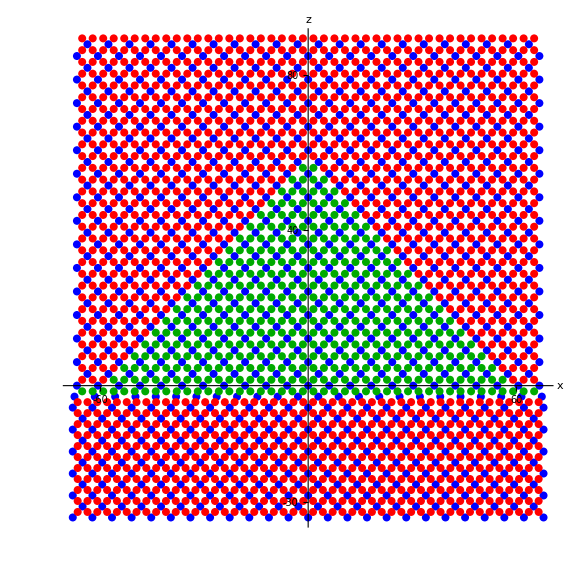
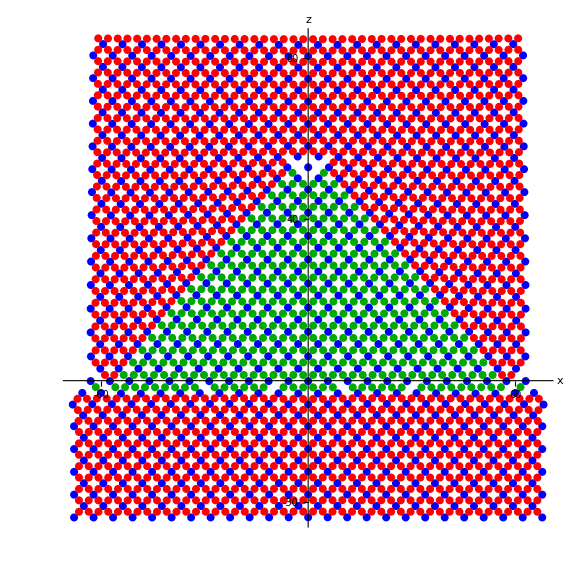
-Graphics3D-  -Graphics3D-
unrel:4*a2/8-Graphics-rel:4*a2/8-Graphics-  

with rp(m,3)in AS_Calc_v2:  

-Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D-


-Graphics- -Graphics- -Graphics- -Graphics-



with msfit=0.03 :  


  -Graphics3D--Graphics3D-

## 2. P70 Fig. 3a

P70-11414616G10-5 Fig.3a
factr=5d+10

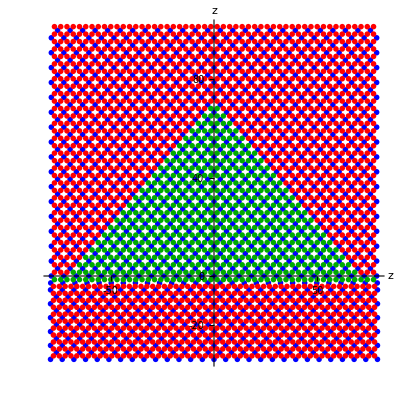
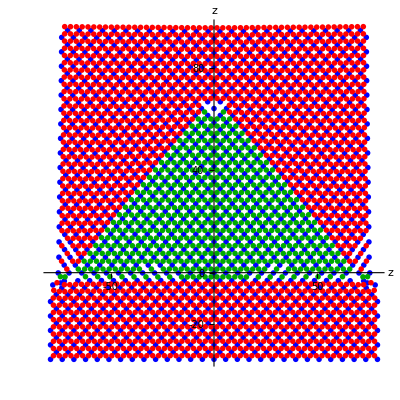
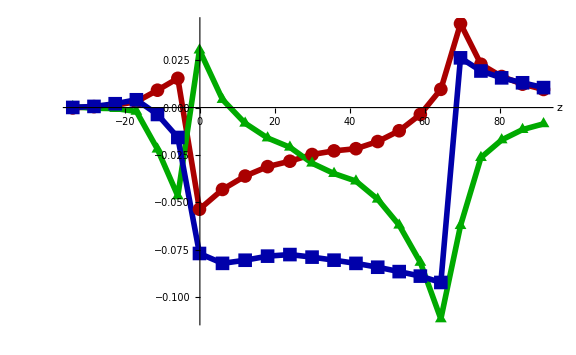
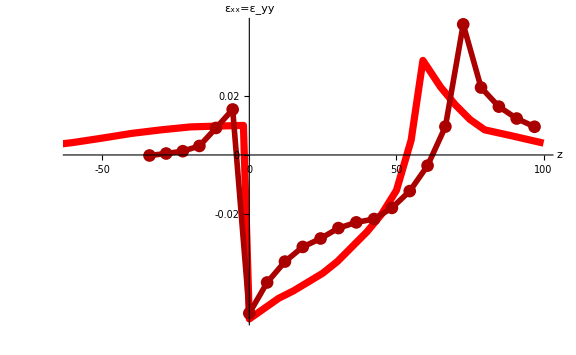
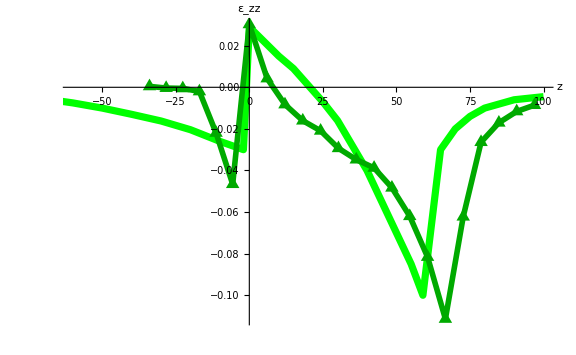
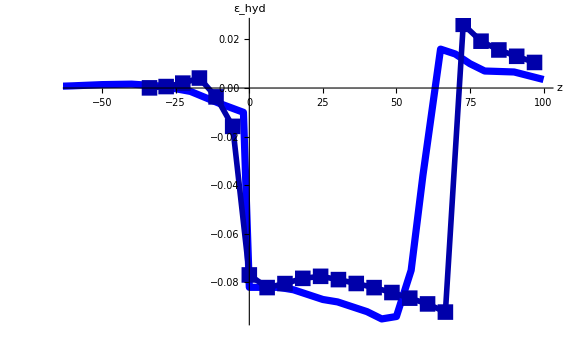
unrel: 4*a2/8-Graphics-   rel: 4*a2/8  -Graphics-  
-Graphics- 
msfit=0.075
-Graphics3D-  
Grundmann: -Graphics--Graphics--Graphics-

## 3. P42 Figs.: 3b, 5a, 5b, both parts of 5c, 5d, 5e

P42-11010612G10 Figs.: 3b, 5a & parts of 5c, 5d, 5e

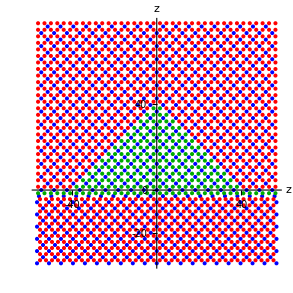
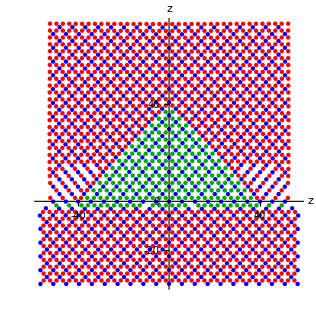
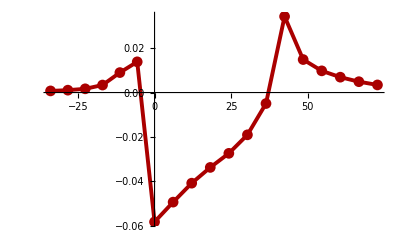
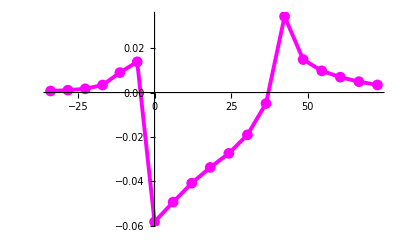
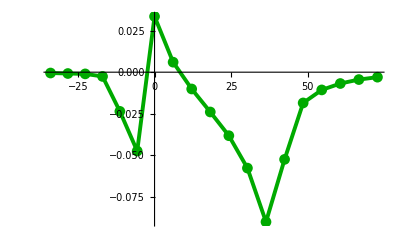
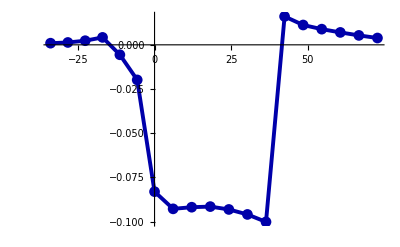
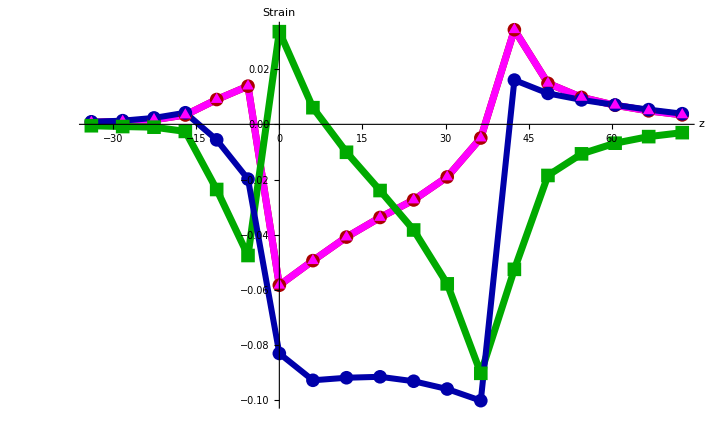
-Graphics3D-unrel:4*a2/8-Graphics-rel:4*a2/8-Graphics- 
  -Graphics--Graphics--Graphics--Graphics-
-Graphics-  -Graphics3D-

P42-1101067G10 Figs.: 5b & parts of 5c, 5d, 5e

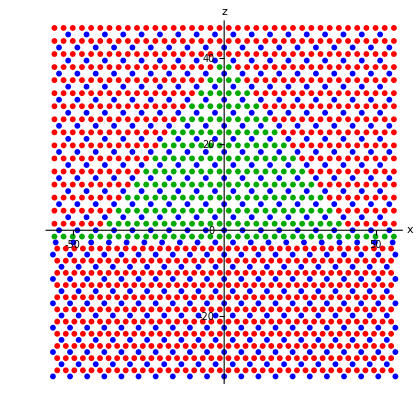
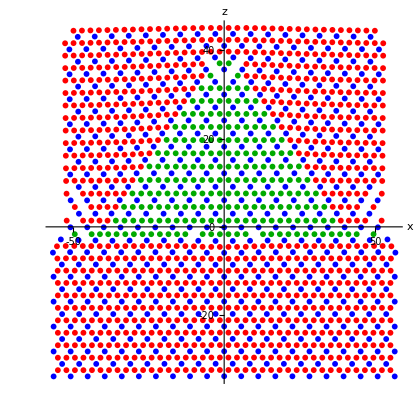
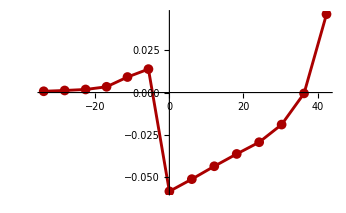
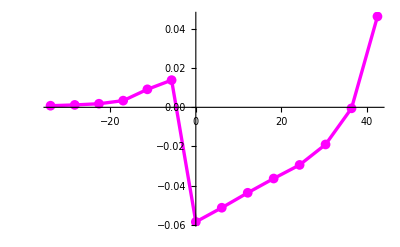
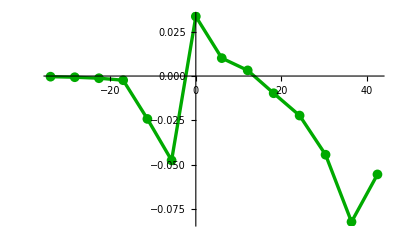
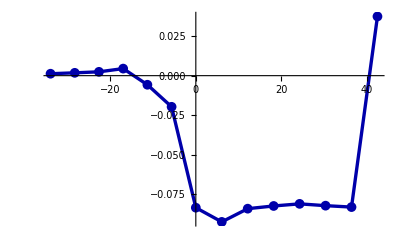
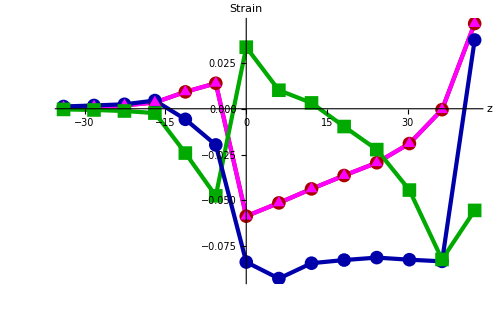
-Graphics3D- unrel:4*a2/8-Graphics-rel:4*a2/8-Graphics-  -Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics--Graphics-

Figs.: 5a, 5b, both parts of 5c, 5d, 5e

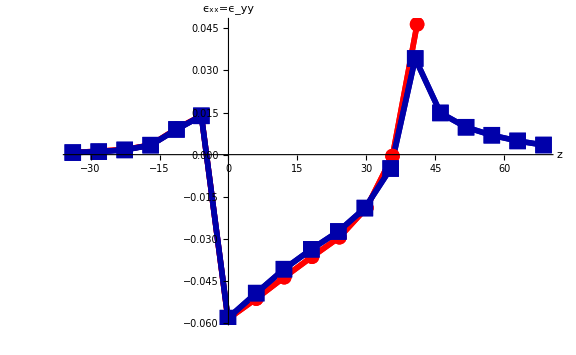
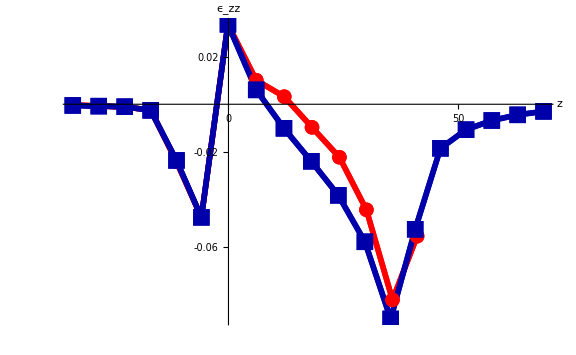
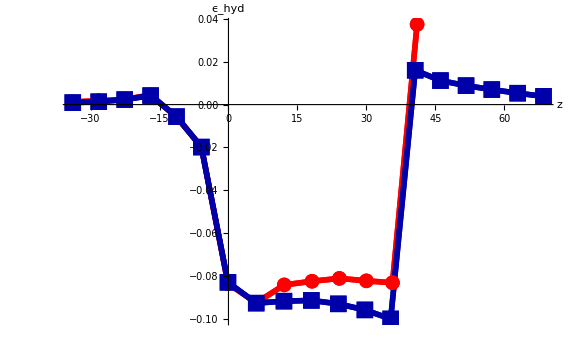

## 4. P21 Fig. 3c

P21-18866G10 Fig.3c

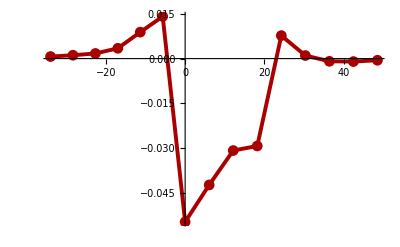
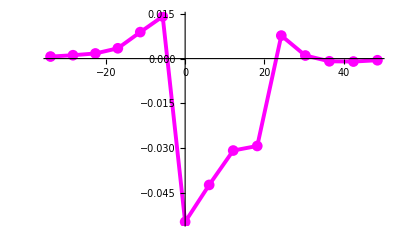
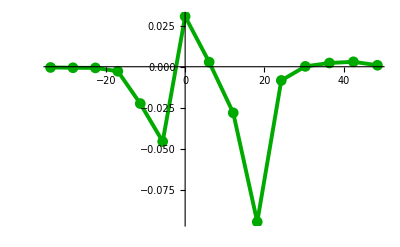
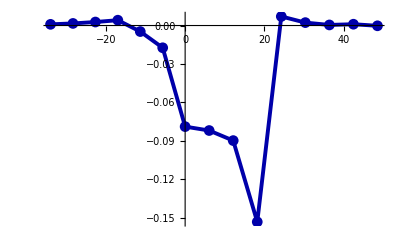
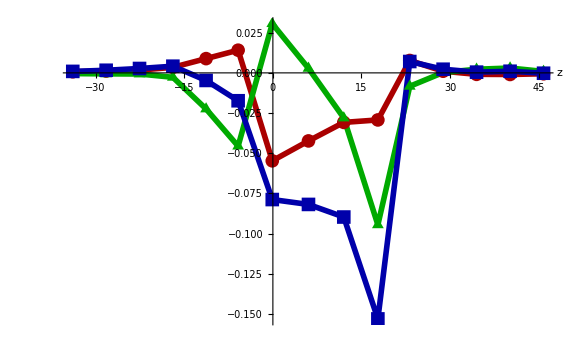
with rp(m,3):
 -Graphics--Graphics--Graphics--Graphics--Graphics- 
msfit=0.075-Graphics3D-

## 5. T24-15 Figs.: 4a, 4b, 4c, 4d, 6b, 6d

T24-15_11111613G10 Figs.: 4a, 4b, 4c, 4d, 6b, 6d

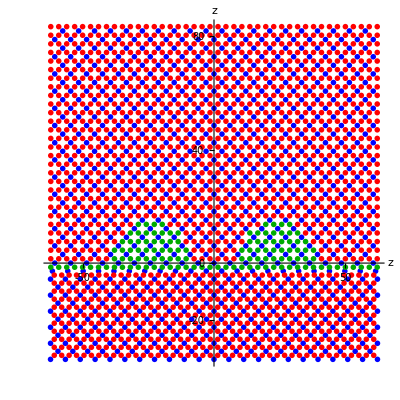
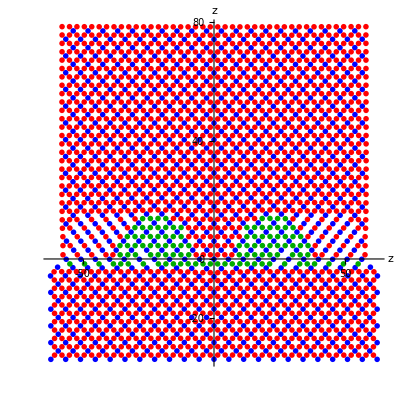
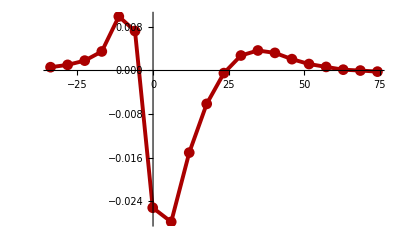
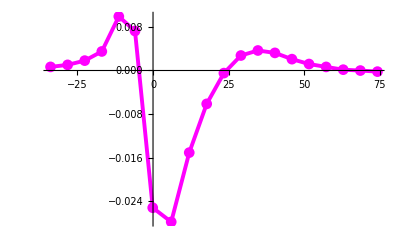
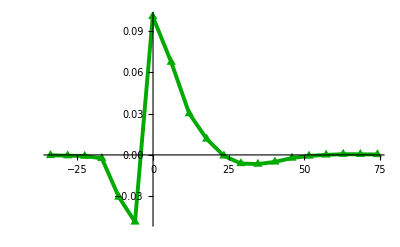
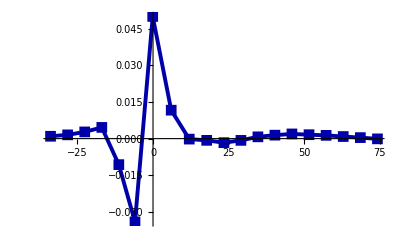
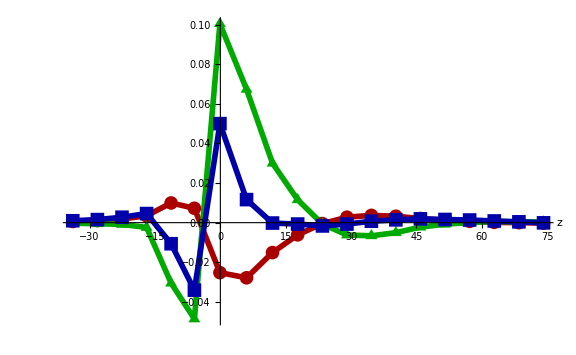
InAs/GaAs, half-torus, Rt=24A, Rq=15A. 
As-blue, In-green, Ga-red. eps_xx-brown, eps_yy-magenta, eps_zz-green, eps_hyd-blue.
WL=a2/2, #atoms: nx=ny=11, nz=6,nz=13.
-Graphics3D-
unrel: 4*a2/8-Graphics-   rel: 4*a2/8  -Graphics-

-Graphics--Graphics--Graphics--Graphics- -Graphics-
msfit=0.075
   -Graphics3D--Graphics3D-

## 6. CSInAs-CSQD Figs.: 4e, 4f, 4g, 6g?

CS20InAs-CSQD1-14more than 10 function - similar to Barettin for InAs/GaAs, Figs.4e, 4f, 4g, 6e?

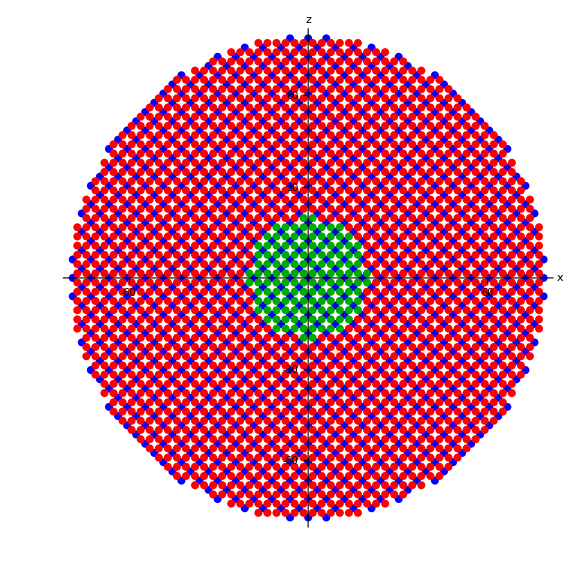
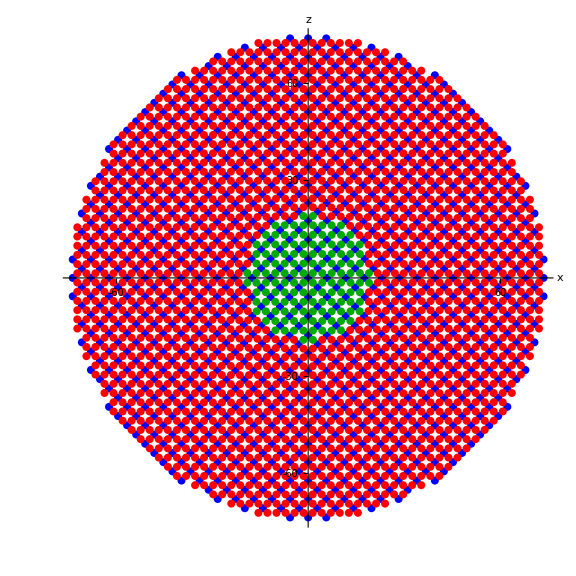
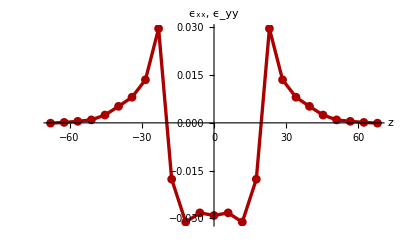
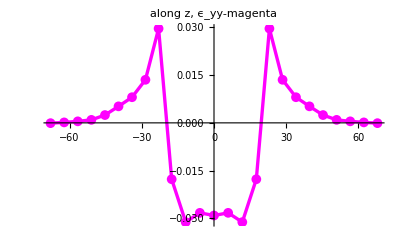
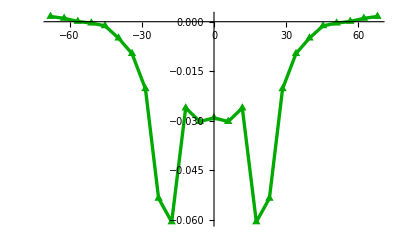
a1=5.6533 for GaAs matrix - out;
a2=6.0584 for InAs - in;
layer thickness = a2/2.
 unrel: 4*a2/8  -Graphics-   rel: 4*a2/8 -Graphics-
 
 
-Graphics--Graphics-  -Graphics- -Graphics--Graphics-



Barettin:
-Graphics- -Graphics- -Graphics-

-Graphics3D- -Graphics3D-




misfit: 0.032 for all atoms

CS19InAs-CSQD1-13 - similar to Barettin for InAs/GaAs, Figs.4e, 4f, 4g, 6e?

a1=5.6533 for GaAs matrix - out;
a2=6.0584 for InAs - in;
layer thickness = a2/2.
 unrel: 4*a2/8  -Graphics-   rel: 4*a2/8 -Graphics-
 
 

-Graphics--Graphics--Graphics--Graphics--Graphics-




Barettin:
-Graphics- -Graphics- -Graphics-





-Graphics3D-
                      -Graphics3D-
misfit: 0.073 for all atoms					                             misfit: 0.073 for As & Ga, and 0.032 for In

## 7. Truncated Cone

TC42-25_11010612

InAs/GaAs, half-torus, Rc=42, h=42, htc=25. 
As-blue, In-green, Ga-red. eps_xx-brown, eps_yy-magenta, eps_zz-green, eps_hyd-blue.
WL=a2/2, #atoms: nx=ny=10, nz=6,nz=12.
write(3401,*)rpr(m,3),epsxx(m);

-Graphics3D-  -Graphics3D-

 unrel: 4*a2/8  -Graphics-   rel: 4*a2/8 -Graphics-  




-Graphics--Graphics--Graphics--Graphics-
-Graphics-

msfit=0.073
-Graphics3D- -Graphics3D-

TC30-33_199610

InAs/GaAs, half-torus, Rct=30, ht=33, htc=18. 
As-blue, In-green, Ga-red. eps_xx-brown, eps_yy-magenta, eps_zz-green, eps_hyd-blue.
WL=a2/2, #atoms: nx=ny=9, nz=6,nz=10.
write(3401,*)rpr(m,3),epsxx(m);

-Graphics3D-  -Graphics3D-

 unrel: 4*a2/8  -Graphics-   rel: 4*a2/8 -Graphics-  




-Graphics--Graphics--Graphics--Graphics- -Graphics- -Graphics-
Barettin, Fig.23
-Graphics-

msfit=0.073
-Graphics3D- -Graphics3D-